# Exact calculation of the partition function of the two-dimensional Ising model on an n × m square lattice.

This Mathematica code calculates the exact partition function of the two-dimensional Ising model on an n × m square lattice with periodic boundary conditions. Copyright: Paul D. Beale,  2010. 

The code is based on:
 	Paul D. Beale, Phys. Rev. Lett. 76, 78 (1996),
  		and Section 13.4.A of 
 	R.K. Pathria and Paul D. Beale, Statistical Mechanics, Third Edition (Academic, Boston, 2011).

The user's input parameters are two positive integers n and m specifying the numbers of rows and columns of the square lattice. The code has been tested on lattice sizes up to 128 × 128.
 
 The code calculates:
     
    	 z = Sum[g[[q + 1]] x^(2 q), {q, 0, n m}] = partition function defined in 
    	 	Pathria and Beale, equations 13.4.56, and 13.4.57 or 13.4.58
     
 	g[[q + 1]] = partition function coefficient which gives the number of microconfigurations with 
 		energy 4qJ above the ground state.
 		
 	x = Exp[-2K] is the Boltzmann factor for a single spin flip where K=J/kT
    
 	s[[q + 1]]=Log[g[[q+1]]] = microcanonical entropy for energy 4qJ above the ground state. 
 		The value of s=-∞ for some values of q since there are no states with that energy.
     
 
This code may be used for noncommercial purposes by referencing:
 	Paul D. Beale, Phys. Rev. Lett. 76, 78 (1996),
  		and
 	R.K. Pathria and Paul D. Beale, Statistical Mechanics, Third Edition (Academic, Boston, 2011).

The software is provided AS IS without warranty of any kind. 

Input n and m and evaluate the cell: 
	n is the number of rows and m is the number of columns. 
	The case n=1 (or m=1) gives the one-dimensional Ising model.

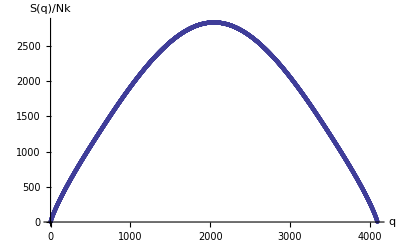

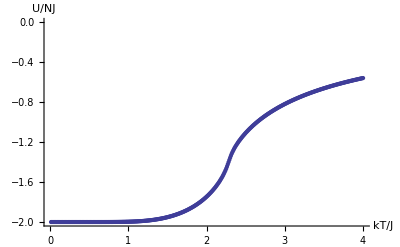

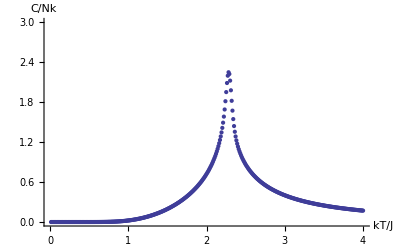

s={0.69314718055994530942,-∞,9.0109133472792890224,9.7040605278392343318,16.637727188605872309,18.023290466471560252,23.864175877654818769,25.651567244818553006,30.810855251067725337,32.877537249490526307,37.544906755735258902,39.819928229734904342,44.109397930776976704,46.544190574533758566,50.53424031449418162,53.092009729125649077,56.841177744595222017,59.492354818668285298,63.046423183481718818,65.766561577064404822,69.162241131156912427,71.930998149113428788,75.198010440190671049,77.998598577001477868,81.160998109778958635,83.979809329207352622,87.056943279440093606,89.88320805984141097,92.890496498291744058,95.715928487934353251,98.665541002515224951,101.48396496592525179,104.38541863323189583,107.1923990383528437,110.05308223812865101,112.84557315711044749,115.67119469103361349,118.44722696919707397,121.24219145481355601,124.00060592489511873,126.76831968468851292,129.50854862875705689,132.25166308652965293,134.97355739377622466,137.694158614804813,140.39785528461818086,143.09760876670984967,145.78343220476210623,148.46369163392333991,151.13208209296910168,153.79396985462516527,156.44543293377904511,159.08989900051232893,161.72497099635582467,164.35283559778969261,166.97206046894998421,169.58404481441575299,172.18795944185023199,174.78470777751222699,177.37383300645954795,179.95592846919329752,182.53076408078475441,185.09874015836406296,187.65976244084424546,190.21411134440470207,192.7617723311815632,195.30295120776148697,197.83767894300531188,200.36611457850691162,202.8883139822460973,205.40440644567160023,207.91446049877111914,210.41858603767986385,212.91685710908906086,215.40937050821539626,217.89620171545073795,220.37743826315178228,222.85315480208225505,225.32343196361136918,227.78834237259028661,230.24796123844028351,232.70235857995954798,235.15160513692534986,237.59576809095915496,240.03491434980290287,242.46910821939457844,244.89841322377131767,247.32289085690177121,249.7426015919765807,252.15760422545477526,254.56795644038378857,256.97371447214011787,259.3749334276209602,261.77166712381843765,264.1639682737984966,266.55188841688531381,268.93547803196296941,271.31478651534219386,273.6898622542221878,276.06075262870862215,278.42750406315917958,280.79016203988462731,283.14877113791368945,285.50337505185872866,287.85401662322928639,290.20073786111537998,292.54357996882189581,294.88258336469673316,297.21778770560321791,299.54923190709431804,301.87695416457387251,304.20099197246803504,306.52138214357210717,308.83816082709760474,311.15136352651231397,313.46102511645283402,315.76717985926292619,318.06986142081335976,320.36910288588651132,322.66493677296721461,324.95739504858833391,327.24650914116328598,329.53230995438673344,331.81482788017928246,334.09409281122369237,336.37013415308888189,338.64298083597210675,340.91266132606477793,343.17920363656334412,345.44263533833447926,347.70298357025108993,349.96027504920960186,352.21453607984214437,354.46579256393414171,356.71407000955905481,358.95939353994032641,361.20178790205093373,363.44127747495995285,365.67788627793549785,367.91163797831274113,370.14255589913551721,372.37066302657953361,374.59598201716495027,376.81853520476570943,379.03834460742272452,381.25543193396771749,383.46981859046423016,385.6815256864720567,387.89057404114109766,390.09698418914038826,392.30077638642782622,394.50197061586590156,396.70058659268852216,398.89664376982382758,401.09016134307769266,403.28115825618243937,405.46965320571510119,407.65566464588941743,409.83921079322557579,412.02030963110156898,414.19897891418988586,416.37523617278311835,418.549098717011932,420.72058364095872088,422.88970782667014532,425.05648794807163434,427.22094047478682265,429.38308167586478511,431.54292762341782864,433.70049419617250349,435.85579708293640099,438.00885178598321505,440.15967362435845721,442.30827773710813242,444.45467908643260242,446.59889246076778709,448.74093247779578056,450.88081358738688798,453.01855007447502116,455.15415606186832592,457.28764551299685125,459.4190322345990103,461.54832987934852508,463.67555194842349108,465.8007117940191446,467.92382262180586374,470.04489749333388459,472.16394932838616646,474.28099090728079378,476.39603487312425832,478.50909373401692263,480.62017986521192447,482.72930551122874275,484.83648278792260698,486.94172368451089584,489.04504006555763498,491.14644367291716987,493.24594612763805686,495.34355893182818361,497.43929347048209972,499.53316101327150837,501.6251727162998419,503.71533962382181604,505.80367266992883148,507.89018268020106558,509.97488037332707206,512.05777636269168303,514.13888115793298415,516.2182051664691116,518.29575869499559789,520.37155195095397273,522.44559504397230488,524.51789798727835153,526.58847069908596281,528.6573230039553708,530.72446463412797485,532.78990523083621779,534.85365434558913126,536.91572144143411229,538.97611589419547775,541.03484699369032855,543.09192394492224063,545.14735586925328595,547.20115180555487318,549.25332071133788418,551.30387146386257026,553.35281286122865914,555.40015362344611215,557.44590239348695915,559.49006773831862767,561.53265814991917175,563.57368204627479534,565.61314777236005499,567.65106360110111641,569.6874377343224301,571.72227830367718158,573.7555933715618629,575.78739093201530322,577.81767891160248767,579.84646517028348532,581.87375750226779932,583.8995636368544441,585.92389123925804704,587.94674791142126487,589.96814119281379748,591.98807856121827518,594.00656743350328862,596.0236151663838239,598.03922905716935915,600.05341634449987261,602.06618420907000615,604.07753977434162246,606.08749010724498828,608.09604221886881059,610.10320306513934739,612.10897954748880912,614.11337851351326226,616.11640675762024099,618.11807102166626866,620.11837799558448561,622.11733431800257559,624.11494657685117856,626.11122130996297328,628.10616500566260886,630.09978410334766054,632.09208499406078073,634.08307402105321269,636.07275748033983025,638.06114162124586361,640.04823264694546716,642.03403671499228244,644.01855993784214534,646.00180838336808377,647.98378807536774859,649.96450499406341749,651.94396507659470852,653.92217421750413694,655.89913826921564608,657.87486304250624021,659.8493543069708446,661.82261779148051522,663.79465918463411795,665.76548413520359459,667.73509825257293051,669.70350710717093631,671.67071623089795346,673.63673111754659165,675.60155722321660328,677.56519996672399827,679.52766473000450038,681.4889568585114439,683.44908166160820781,685.40804441295528218,687.36585035089205992,689.32250467881344506,691.27801256554136652,693.23237914569128522,695.18560952003377974,697.13770875585129486,699.08868188729013499,701.03853391570778322,702.98726981001562487,704.93489450701715313,706.88141291174173256,708.82682989777399488,710.77115030757894006,712.71437895282281402,714.65652061468983334,716.59758004419482547,718.53756196249185195,720.4764710611788808,722.41431200259857284,724.35108942013524551,726.28680791850807671,728.22147207406060967,730.15508643504661896,732.08765552191239659,734.0191838275755158,735.94967581770012944,737.8791359309688584,739.80756857935132479,741.73497814836938342,743.66136899735910405,745.58674545972955626,747.51111184321844734,749.4344724301446631,751.35683147765776038,753.27819321798445918,755.1985618586721814,757.11794158282968262,759.03633654936482201,760.95375089321951517,762.87018872560191354,764.78565413421585336,766.70015118348761652,768.61368391479004458,770.52625634666404689,772.43787247503754274,774.34853627344187684,776.25825169322574678,778.16702266376668058,780.07485309268010135,781.98174686602601597,783.88770784851336375,785.79273988370206041,787.69684679420277229,789.60003238187445493,791.50230042801968973,793.40365469357785171,795.30409891931614083,797.20363682601850901,799.1022721146725141,801.0000084666541318,802.89684954391055594,804.79279898914101696,806.68786042597564812,808.58203745915242817,810.47533367469222913,812.36775264007199712,814.25929790439609364,816.14997299856582469,818.03978143544718406,819.92872671003683735,821.81681229962637228,823.70404166396484092,825.59041824541961869,827.4759454691356049,829.36062674319278896,831.24446545876220625,833.127464990260307,835.00962869550176149,836.89095991585072424,838.77146197637057975,840.65113818597219171,842.52999183756067773,844.4080262081807308,846.28524455916050875,848.16165013625411256,850.03724616978267394,851.91203587477407251,853.78602245110130247,855.65920908361950847,857.53159894230171,859.40319518237323345,861.27400094444487069,863.14401935464478278,865.01325352474916706,866.88170655231170582,868.74938152079181436,870.61628149968170606,872.4824095446322918,874.34776869757793107,876.21236198686005148,878.07619242734965363,879.93926302056871779,881.80157675481052874,883.66313660525893491,885.52394553410655784,887.38400649067196772,889.24332241151584062,891.10189622055611285,892.9597308291821478,894.81682913636793031,896.67319402878430359,898.52882838091026361,900.38373505514332547,902.23791690190897661,904.09137675976923103,905.94411745553029906,907.79614180434938683,909.64745260984063961,911.49805266418024295,913.34794474821069578,915.19713163154426903,917.04561607266566392,918.89340081903388331,920.74048860718333005,922.58688216282414573,924.43258420094180362,926.27759742589596913,928.12192453151864152,929.96556820121159018,931.80853110804309908,933.65081591484403286,935.49242527430323809,937.33336182906229312,939.17362821180962022,941.01322704537397352,942.85216094281731634,944.6904325075271017,946.52804433330796978,948.36499900447287597,950.20129909593366381,952.03694717329109636,953.87194579292436068,955.70629750208005912,957.54000483896070232,959.373070332812718,961.20549650401399056,963.03728586416094609,964.86844091615519798,966.69896415428976816,968.52885806433489948,970.35812512362347482,972.18676780113605865,974.01478855758557713,975.84218984550165305,977.66897410931461207,979.49514378543917707,981.32070130235786755,983.14564908070412148,984.96998953334515719,986.79372506546459297,988.61685807464484274,990.43939095094930616,992.26132607700437189,994.082665828081253,995.90341257217767404,997.72356867009942922,999.54313647554183181,1001.3621183351710749,1003.1805165887055242,1004.9983335689969634,1006.8155716021118138,1008.6322330074123488,1010.448320097637926,1012.263835178986257,1014.0787805511947396,1015.8931585076218719,1017.7069713353287731,1019.5202213151608321,1021.332910721829508,1023.1450418239943033,1024.9566168843449357,1026.7676381596837283,1028.5781079010082429,1030.3880283535941794,1032.1974017570785617,1034.0062303455432353,1035.8145163475986967,1037.6222619864682769,1039.4294694800727007,1041.236141041115041,1043.042278877166091,1044.84788519075017,1046.6529621794313847,1048.457512035900361,1050.2615369480614645,1052.0650390991205234,1053.8680206676730691,1055.6704838277931055,1057.4724307491224186,1059.2738635969604344,1061.0747845323546326,1062.8751957121915194,1064.6750992892881632,1066.4744974124842904,1068.2733922267349397,1070.0717858732036673,1071.869680489356293,1073.6670782090551742,1075.4639811626539893,1077.2603914770930099,1079.0563112759948352,1080.8517426797605566,1082.6466878056663189,1084.4411487679602336,1086.2351276779595997,1088.0286266441483766,1089.8216477722748507,1091.6141931654494277,1093.4062649242424773,1095.1978651467821487,1096.9889959288520665,1098.7796593639888092,1100.5698575435790634,1102.3595925569563362,1104.1488664914971014,1105.9376814327162408,1107.7260394643616349,1109.513942668507745,1111.3013931256480158,1113.0883929147859172,1114.8749441135244314,1116.6610487981537779,1118.4467090437371548,1120.2319269241942647,1122.0167045123823733,1123.8010438801746407,1125.5849470985354446,1127.3684162375924042,1129.1514533667047937,1130.9340605545280207,1132.7162398690738285,1134.4979933777658617,1136.2793231474902225,1138.060231244640623,1139.8407197351577249,1141.6207906845622388,1143.4004461579813387,1145.17968822016793,1146.9585189355122901,1148.7369403680455863,1150.5149545814347551,1152.292563638968214,1154.0697696035318552,1155.8465745375747604,1157.6229805030640551,1159.3989895614283083,1161.1746037734888679,1162.9498251993785109,1164.7246558984467692,1166.4990979291512877,1168.2731533489345535,1170.04682421408533,1171.8201125795841207,1173.5930204989319795,1175.3655500239619811,1177.1377032046326611,1178.9094820888027334,1180.6808887219863956,1182.4519251470885315,1184.2225934041191309,1185.9928955298862485,1187.7628335576668383,1189.5324095168548107,1191.3016254325856756,1193.0704833253371533,1194.8389852105051585,1196.6071330979545844,1198.3749289915443464,1200.1423748886261733,1201.909472779516672,1203.6762246469422288,1205.4426324654563541,1207.2086982008291253,1208.9744238094084294,1210.7398112374527658,1212.5048624204354243,1214.2695792823199171,1216.0339637348066107,1217.7980176765505695,1219.5617429923507016,1221.325141552310371,1223.0882152109697223,1224.8509658064100482,1226.613395159330619,1228.3755050720984807,1230.1372973277718266,1231.8987736890976379,1233.6599358974843925,1235.4207856719507382,1237.1813247080511308,1238.9415546767795391,1240.7014772234524269,1242.4610939665723232,1244.2204064966734001,1245.9794163751505821,1247.7381251330738129,1249.496534269989213,1251.2546452527089559,1253.0124595140917966,1254.7699784518162758,1256.5272034271487187,1258.2841357637082345,1260.0407767462310067,1261.7971276193362409,1263.5531895862962129,1265.3089638078129219,1267.0644514008039163,1268.8196534371999105,1270.574570942756855,1272.3292048958851585,1274.0835562264987866,1275.8376258148869829,1277.591414490611361,1279.3449230314311196,1281.0981521622591189,1282.8511025541515338,1284.6037748233337668,1286.3561695302652632,1288.1082871787458108,1289.8601282150658486,1291.6116930272032275,1293.362981944068784,1295.1139952348029895,1296.8647331081258308,1298.6151957117419646,1300.3653831318030585,1302.1152953924291007,1303.8649324552903158,1305.6142942192511741,1307.3633805200778243,1309.1121911302101148,1310.8607257585992002,1312.608984050611553,1314.356965588000023,1316.1046698889424033,1317.8520964081477785,1319.5992445370307424,1321.3461136039533857,1323.0927028745347698,1324.8390115520274112,1326.5850387777601236,1328.3307836316463781,1330.0762451327571673,1331.8214222399571852,1333.5663138526029671,1335.3109188113014711,1337.0552358987274287,1338.7992638404976453,1340.5430013061002883,1342.286446909877074,1344.0295992120561384,1345.7724567198332686,1347.515017888499065,1349.2572811226095156,1350.9992447771973796,1352.7409071590217077,1354.4822665278527658,1356.2233210977895786,1357.964069038607272,1359.7045084771313638,1361.4446374986361374,1363.1844541482642216,1364.9239564324645094,1366.6631423204455544,1368.4020097456416139,1370.1405566071885316,1371.8787807714067013,1373.6166800732883957,1375.3542523179868051,1377.0914952823041924,1378.8284067161766446,1380.5649843441529742,1382.3012258668654115,1384.0371289624898121,1385.7726912881931997,1387.50791048156656,1389.2427841620409003,1390.9773099322846945,1392.7114853795809358,1394.4453080771821278,1396.1787755856416534,1397.9118854541200683,1399.6446352216649765,1401.3770224184632525,1403.1090445670644871,1404.8406991835746353,1406.5719837788189571,1408.3028958594734413,1410.0334329291640084,1411.7635924895328847,1413.4933720412716411,1415.2227690851204811,1416.9517811228334552,1418.6804056581093663,1420.4086401974882162,1422.1364822512131219,1423.8639293340577106,1425.5909789661190728,1427.3176286735764248,1429.0438759894156958,1430.7697184541203177,1432.4951536163285528,1434.2201790334577497,1435.9447922722959653,1437.6689909095614411,1439.3927725324304599,1441.1161347390341521,1442.8390751389248522,1444.5615913535126415,1446.2836810164727387,1448.0053417741244255,1449.7265712857822184,1451.4473672240800135,1453.1677272752689497,1454.8876491394897476,1456.6071305310202914,1458.3261691784992309,1460.0447628251263849,1461.7629092288407296,1463.4806061624767606,1465.1978514139000112,1466.9146427861225116,1468.6309780973989668,1470.346855181304425,1472.0622718867942029,1473.7772260782468222,1475.4917156354907057,1477.205738453815366,1478.9192924439678115,1480.6323755321348776,1482.3449856599121811,1484.0571207842603772,1485.7687788774493865,1487.479957926991241,1489.190655935562185,1490.9008709209146456,1492.6106009157796755,1494.3198439677604504,1496.028598139217386,1497.7368615071454246,1499.4446321630440201,1501.1519082127803365,1502.8586877764461535,1504.5649689882089586,1506.2707499961576855,1507.9760289621435435,1509.680804061616363,1511.3850734834568668,1513.0888354298052617,1514.7920881158865256,1516.4948297698327509,1518.1970586325028902,1519.8987729573002331,1521.5999710099879286,1523.3006510685028537,1525.0008114227681124,1526.700450374504438,1528.399566237040756,1530.0981573351241523,1531.7962220047294783,1533.4937585928688135,1535.1907654574009917,1536.8872409668413869,1538.5831835001721447,1540.2785914466530299,1541.9734632056330567,1543.6677971863630518,1545.3615918078092951,1547.054845498468371,1548.7475566961833552,1550.4397238479614538,1552.1313454097932006,1553.8224198464733149,1555.5129456314233092,1557.2029212465159339,1558.8923451819015349,1560.5812159358363965,1562.2695320145131337,1563.957291931893192,1565.6444942095415086,1567.3311373764633808,1569.0172199689435847,1570.7027405303877808,1572.3876976111662377,1574.0720897684599033,1575.7559155661088455,1577.4391735744630815,1579.1218623702358129,1580.8039805363590766,1582.4855266618418202,1584.1664993416304086,1585.8468971764715621,1587.5267187727777257,1589.2059627424948676,1590.8846277029726988,1592.5627122768373075,1594.240215091866196,1595.9171347808657097,1597.5934699815508415,1599.2692193364273964,1600.9443814926764994,1602.6189551020414246,1604.2929388207167277,1605.966331309239657,1607.6391312323838215,1609.3113372590550906,1610.9829480621896997,1612.6539623186545363,1614.3243787091495785,1615.9941959181124576,1617.6634126336251178,1619.3320275473225413,1621.0000393543035111,1622.6674467530433803,1624.3342484453088174,1626.0004431360744963,1627.6660295334417006,1629.3310063485588099,1630.9953722955436365,1632.6591260914075817,1634.3222664559815781,1635.9847921118437878,1637.6467017842490232,1639.3079942010598592,1640.9686680926794051,1642.6287221919857038,1644.2881552342677276,1645.9469659571629384,1647.6051531005963813,1649.2627154067212812,1650.9196516198611104,1652.5759604864530977,1654.2316407549931482,1655.8866911759821437,1657.5411105018735951,1659.1948974870226152,1660.8480508876361859,1662.5005694617246877,1664.1524519690546668,1665.8036971711028086,1667.4543038310110922,1669.1042707135430975,1670.7535965850414388,1672.4022802133862983,1674.0503203679550333,1675.6977158195828317,1677.3444653405243903,1678.9905677044165924,1680.6360216862421579,1682.280826062294245,1683.9249796101419771,1685.5684811085968743,1687.2113293376801653,1688.8535230785909574,1690.4950611136752445,1692.1359422263957292,1693.7761652013024402,1695.4157288240041234,1697.0546318811403863,1698.6928731603545773,1700.3304514502673786,1701.9673655404510959,1703.6036142214046244,1705.2391962845290749,1706.8741105221040404,1708.5083557272644874,1710.1419306939782544,1711.7748342170241402,1713.4070650919705674,1715.0386221151548043,1716.6695040836627295,1718.2997097953091249,1719.9292380486184818,1721.5580876428063063,1723.1862573777609088,1724.8137460540256654,1726.4405524727817368,1728.066675435831232,1729.6921137455808039,1731.3168662050256651,1732.9409316177340105,1734.5643087878318367,1736.1869965199881447,1737.8089936194005169,1739.4302988917810554,1741.0509111433426725,1742.670829180785723,1744.2900518112849669,1745.9085778424768542,1747.5264060824471222,1749.1435353397186948,1750.7599644232398758,1752.3756921423728279,1753.9907173068823273,1755.6050387269247871,1757.218655213037541,1758.8315655761283788,1760.4437686274653273,1762.0552631786666683,1763.6660480416911867,1765.2761220288286421,1766.8854839526904569,1768.4941326262006137,1770.1020668625867572,1771.7092854753714925,1773.315787278363875,1774.9215710856510864,1776.5266357115902894,1778.1309799708006573,1779.7346026781555727,1781.3375026487749899,1782.9396786980179559,1784.5411296414752851,1786.1418542949623842,1787.7418514745122208,1789.3411199963684324,1790.9396586769785717,1792.5374663329874832,1794.134541781230808,1795.7308838387286119,1797.3264913226791342,1798.9213630504526521,1800.5154978395854588,1802.1088945077739502,1803.7015518728688184,1805.2934687528693475,1806.8846439659178095,1808.4750763302939566,1810.0647646644096077,1811.6537077868033259,1813.2419045161351836,1814.8293536711816139,1816.4160540708303451,1818.0020045340754148,1819.587203880012264,1821.1716509278329048,1822.7553444968211639,1824.338283406347996,1825.9204664758668675,1827.5018925249092071,1829.082560373079922,1830.6624688400529779,1832.2416167455670399,1833.8200029094211743,1835.3976261514706078,1836.9744852916225439,1838.5505791498320341,1840.1259065460979022,1841.7004663004587211,1843.2742572329888402,1844.8472781637944609,1846.4195279130097616,1847.9910053007930676,1849.5617091473230675,1851.1316382727950729,1852.7007914974173211,1854.2691676414073203,1855.8367655249882343,1857.403583968385308,1858.9696217918223308,1860.5348778155181381,1862.0993508596831487,1863.6630397445159398,1865.2259432901998543,1866.7880603168996451,1868.3493896447581499,1869.9099300938930008,1871.4696804843933639,1873.0286396363167109,1874.5868063696856206,1876.1441795044846097,1877.7007578606569933,1879.2565402581017726,1880.8115255166705514,1882.3657124561644787,1883.9190998963312183,1885.471686656861944,1887.0234715573883609,1888.5744534174797503,1890.1246310566400406,1891.6740032943049005,1893.2225689498388564,1894.7703268425324334,1896.3172757915993171,1897.8634146161735394,1899.4087421353066849,1900.9532571679651185,1902.4969585330272349,1904.0398450492807278,1905.5819155354198795,1907.1231688100428708,1908.6636036916491097,1910.2032189986365801,1911.742013549299209,1913.2799861618242521,1914.8171356542896984,1916.3534608446616922,1917.8889605507919733,1919.4236335904153344,1920.957478781147096,1922.4904949404805983,1924.0226808857847096,1925.554035434301352,1927.0845574031430422,1928.6142456092904498,1930.1430988695899703,1931.6711160007513149,1933.1982958193451148,1934.7246371418005415,1936.2501387844029422,1937.7747995632914898,1939.2986182944568478,1940.8215937937388502,1942.3437248768241956,1943.8650103592441554,1945.3854490563722965,1946.9050397834222176,1948.4237813554453003,1949.9416725873284725,1951.4587122937919865,1952.9748992893872103,1954.4902323884944321,1956.0047104053206778,1957.5183321538975423,1959.0310964480790328,1960.5430021015394258,1962.0540479277711367,1963.5642327400826012,1965.0735553515961705,1966.5820145752460183,1968.0896092237760596,1969.5963381097378831,1971.1022000454886941,1972.6071938431892712,1974.1113183148019332,1975.6145722720885193,1977.1169545266083803,1978.6184638897163816,1980.1190991725609186,1981.618859186081942,1983.1177427410089965,1984.6157486478592695,1986.1128757169356518,1987.6091227583248093,1989.1044885818952661,1990.5989719972954981,1992.092571813952039,1993.5852868410675954,1995.0771158876191747,1996.5680577623562225,1998.0581112737987717,1999.5472752302356014,2001.0355484397224078,2002.5229297100799843,2004.0094178488924132,2005.4950116635052676,2006.9797099610238238,2008.4635115483112836,2009.9464152319870083,2011.4284198184247614,2012.9095241137509627,2014.3897269238429525,2015.869027054327265,2017.3474233105779137,2018.8249144977146847,2020.3014994206014419,2021.7771768838444411,2023.2519456917906547,2024.7258046485261056,2026.198752557874212,2027.670788223394141,2029.1419104483791729,2030.6121180358550746,2032.0814097885784832,2033.5497845090352991,2035.0172409994390889,2036.4837780617294975,2037.9493944975706705,2039.4140891083496859,2040.8778606951749949,2042.3407080588748729,2043.8026299999958795,2045.2636253188013283,2046.7236928152697657,2048.1828312890934595,2049.6410395396768969,2051.0983163661352911,2052.5546605672930983,2054.0100709416825435,2055.4645462875421551,2056.9180854028153094,2058.3706870851487843,2059.8223501318913216,2061.2730733400921992,2062.722855506499812,2064.1716954275602621,2065.619591899415958,2067.0665437179042228,2068.5125496785559121,2069.95760857659404,2071.4017192069324148,2072.8448803641742836,2074.2870908426109858,2075.7283494362206153,2077.1686549386666925,2078.6080061432968443,2080.0464018431414936,2081.4838408309125576,2082.9203218990021548,2084.3558438394813215,2085.7904054440987361,2087.2240055042794534,2088.6566428111236469,2090.0883161554053608,2091.5190243275712696,2092.9487661177394478,2094.3775403156981477,2095.8053457109045858,2097.2321810924837389,2098.6580452492271478,2100.0829369695917307,2101.5068550416986049,2102.9297982533319174,2104.3517653919376841,2105.772755244622638,2107.1927665981530857,2108.6117982389537731,2110.0298489531067596,2111.4469175263503008,2112.8630027440777403,2114.2781033913364098,2115.6922182528265385,2117.1053461129001702,2118.5174857555600903,2119.9286359644587602,2121.3387955228972618,2122.7479632138242491,2124.1561378198349101,2125.563318123169936,2126.9695029057144997,2128.3746909489972433,2129.7788810341892736,2131.1820719421031665,2132.5842624531919803,2133.9854513475482775,2135.3856374049031552,2136.7848194046252843,2138.1829961257199576,2139.5801663468281457,2140.9763288462255629,2142.3714824018217407,2143.7656257911591105,2145.1587577914120947,2146.5508771793862069,2147.9419827315171608,2149.3320732238699868,2150.721147432138159,2152.1092041316427293,2153.4962420973314714,2154.8822601037780328,2156.2672569251810961,2157.6512313353635484,2159.03418210777166,2160.4161080154742714,2161.7970078311619899,2163.1768803271463938,2164.5557242753592462,2165.9335384473517174,2167.3103216142936162,2168.6860725469726294,2170.0607900157935712,2171.4344727907776406,2172.8071196415616877,2174.1787293373974892,2175.5493006471510329,2176.91883233930181,2178.287323181942118,2179.6547719427763708,2181.0211773891204189,2182.386538287900878,2183.7508534056544668,2185.1141215085273532,2186.4763413622745103,2187.8375117322590808,2189.1976313834517507,2190.5566990804301314,2191.9147135873781519,2193.2716736680854592,2194.6275780859468277,2195.9824256039615786,2197.3362149847330072,2198.6889449904678204,2200.0406143829755823,2201.3912219236681698,2202.740766373559237,2204.0892464932636886,2205.436661042997163,2206.7830087825755241,2208.1282884714143626,2209.4724988685285069,2210.8156387325315421,2212.1577068216353399,2213.4987018936495968,2214.8386227059813814,2216.1774680156346924,2217.5152365792100242,2218.8519271529039434,2220.1875384925086742,2221.5220693534116925,2222.8555184905953311,2224.1878846586363927,2225.5191666117057736,2226.8493631035680964,2228.1784728875813525,2229.5064947166965537,2230.8334273434573944,2232.1592695199999221,2233.4840199980522192,2234.8076775289340927,2236.1302408635567751,2237.4517087524226342,2238.772079945624893,2240.0913531928473594,2241.4095272433641654,2242.7266008460395167,2244.0425727493274517,2245.3574417012716104,2246.6712064495050138,2247.9838657412498527,2249.2954183233172867,2250.6058629421072529,2251.9151983436082856,2253.2234232733973446,2254.5305364766396551,2255.836536698088557,2257.1414226820853638,2258.4451931725592333,2259.7478469130270469,2261.0493826465933,2262.3497991159500029,2263.649095063376591,2264.9472692307398468,2266.2443203594938309,2267.5402471906798246,2268.835048464926282,2270.1287229224487931,2271.4212693030500575,2272.7126863461198687,2274.0029727906351082,2275.2921273751597513,2276.5801488378448831,2277.8670359164287252,2279.1527873482366727,2280.4374018701813433,2281.7208782187626355,2283.003215130067799,2284.2844113397715153,2285.5644655831359893,2286.8433765950110523,2288.1211431098342751,2289.3977638616310932,2290.6732375840149423,2291.9475630101874053,2293.2207388729383702,2294.4927639046461994,2295.7636368372779101,2297.0333564023893659,2298.3019213311254803,2299.5693303542204304,2300.835582201997883,2302.1006756043712321,2303.3646092908438469,2304.6273819905093325,2305.8889924320518015,2307.1494393437461573,2308.408721453458389,2309.6668374886458782,2310.9237861763577175,2312.1795662432350403,2313.434176415511363,2314.6876154190129389,2315.9398819791591238,2317.1909748209627535,2318.440892669030534,2319.6896342475634426,2320.937198280357142,2322.1835834908024061,2323.4287886018855583,2324.6728123361889214,2325.9156534158912804,2327.1573105627683573,2328.3977824981932984,2329.637067943137174,2330.8751656181694901,2332.1120742434587133,2333.3477925387728079,2334.5823192234797856,2335.8156530165482677,2337.0477926365480605,2338.2787368016507428,2339.5084842296302664,2340.73703363786357,2341.9643837433312052,2343.1905332626179756,2344.4154809119135895,2345.6392254070133248,2346.8617654633187078,2348.0830997958382042,2349.3032271191879244,2350.522146147592341,2351.7398555948850206,2352.9563541745093678,2354.1716405995193839,2355.385713582580438,2356.5985718359700519,2357.8102140715786993,2359.0206390009106173,2360.2298453350846326,2361.4378317848350012,2362.6445970605122615,2363.8501398720841018,2365.0544589291362412,2366.2575529408733248,2367.4594206161198327,2368.660060663321003,2369.8594717905437693,2371.057652705477712,2372.2546021154360238,2373.4503187273564898,2374.6448012478024816,2375.8380483829639662,2377.0300588386585287,2378.2208313203324106,2379.4103645330615613,2380.5986571815527053,2381.7857079701444239,2382.9715156028082509,2384.1560787831497845,2385.3393962144098124,2386.5214665994654534,2387.7022886408313129,2388.8818610406606539,2390.060182500746583,2391.2372517225232517,2392.4130674070670727,2393.5876282550979519,2394.7609329669805351,2395.9329802427254707,2397.1037687819906878,2398.2732972840826894,2399.4415644479578619,2400.6085689722237994,2401.7743095551406448,2402.9387848946224455,2404.101993688238526,2405.2639346332148758,2406.4246064264355533,2407.5840077644441064,2408.7421373434450081,2409.8989938593051092,2411.0545760075551071,2412.2088824833910304,2413.3619119816757403,2414.5136631969404485,2415.6641348233862513,2416.8133255548856804,2417.9612340849842706,2419.1078591069021434,2420.2531993135356085,2421.3972533974587814,2422.5400200509252179,2423.6814979658695656,2424.821685833909233,2425.9605823463460749,2427.0981861941680957,2428.2344960680511691,2429.3695106583607758,2430.5032286551537586,2431.6356487481800945,2432.7667696268846844,2433.8965899804091608,2435.0251084975937127,2436.1523238669789283,2437.2782347768076561,2438.4028399150268826,2439.5261379692896291,2440.6481276269568665,2441.7688075750994467,2442.8881765005000544,2444.0062330896551751,2445.1229760287770826,2446.2384040037958446,2447.3525157003613461,2448.4653098038453325,2449.57678499934347,2450.6869399716774256,2451.7957734053969656,2452.9032839847820723,2454.0094703938450804,2455.1143313163328319,2456.21786543572885,2457.3200714352555322,2458.4209479978763627,2459.5204938062981435,2460.6187075429732456,2461.715587890101879,2462.8111335296343819,2463.9053431432735305,2464.9982154124768675,2466.08974901845905,2467.1799426421942187,2468.2687949644183848,2469.3563046656318388,2470.4424704261015778,2471.5272909258637536,2472.610764844726141,2473.6928908622706255,2474.7736676578557126,2475.8530939106190559,2476.9311682994800073,2478.0078895031421859,2479.0832562000960691,2480.1572670686216036,2481.2299207867908369,2482.3012160324705702,2483.3711514833250319,2484.4397258168185721,2485.5069377102183779,2486.5727858405972105,2487.6372688848361625,2488.7003855196274377,2489.762134421477151,2490.8225142667081505,2491.881523731462861,2492.939161491706149,2493.9954262232282094,2495.0503166016474736,2496.1038313024135403,2497.1559690008101271,2498.2067283719580447,2499.2561080908181934,2500.304106832194581,2501.3507232707373634,2502.3959560809459075,2503.4398039371718761,2504.4822655136223359,2505.5233394843628871,2506.5630245233208165,2507.6013193042882727,2508.6382225009254644,2509.6737327867638812,2510.7078488352095376,2511.7405693195462399,2512.7718929129388762,2513.8018182884367295,2514.8303441189768138,2515.8574690773872344,2516.88319183639057,2517.9075110686072802,2518.9304254465591347,2519.9519336426726677,2520.9720343292826547,2521.990726178635614,2523.0080078628933315,2524.0238780541364099,2525.0383354243678416,2526.0513786455166055,2527.0630063894412886,2528.0732173279337314,2529.0820101327226975,2530.0893834754775682,2531.0953360278120609,2532.0998664612879727,2533.1029734474189479,2534.1046556576742711,2535.1049117634826845,2536.10374043623623,2537.1011403472941169,2538.097110167986614,2539.091648569618967,2540.0847542234753412,2541.0764258008227895,2542.0666619729152453,2543.0554614109975418,2544.0428227863094554,2545.028744770089776,2546.0132260335804022,2546.9962652480304625,2547.977861084700462,2548.9580122148664556,2549.9367173098242466,2550.9139750408936114,2551.8897840794225507,2552.8641430967915664,2553.8370507644179651,2554.8085057537601878,2555.7785067363221662,2556.747052383657705,2557.7141413673748917,2558.6797723591405317,2559.6439440306846115,2560.6066550538047878,2561.5679041003709038,2562.5276898423295322,2563.4860109517085457,2564.4428661006217142,2565.398253961273329,2566.3521732059628546,2567.3046225070896078,2568.2556005371574641,2569.2051059687795913,2570.1531374746832109,2571.0996937277143872,2572.0447734008428438,2572.9883751671668078,2573.9304976999178823,2574.8711396724659462,2575.8102997583240823,2576.7479766311535333,2577.6841689647686857,2578.6188754331420824,2579.5520947104094633,2580.4838254708748335,2581.4140663890155611,2582.3428161394875026,2583.2700733971301567,2584.1958368369718476,2585.1201051342349358,2586.0428769643410585,2586.964151002916398,2587.8839259257969798,2588.8022004090339988,2589.718973128899175,2590.6342427618901378,2591.5480079847358401,2592.4602674744020006,2593.3710199080965761,2594.2802639632752627,2595.1879983176470265,2596.0942216491796638,2596.9989326361053904,2597.9021299569264607,2598.8038122904208166,2599.7039783156477657,2600.6026267119536892,2601.4997561589777799,2602.3953653366578096,2603.2894529252359268,2604.1820176052644843,2605.0730580576118963,2605.9625729634685263,2606.8505610043526045,2607.7370208621161756,2608.621951218951077,2609.505350757394947,2610.3872181603372636,2611.2675521110254131,2612.1463512930707902,2613.0236143904549273,2613.8993400875356554,2614.7735270690532953,2615.6461740201368786,2616.517279626310401,2617.3868425734991047,2618.2548615480357927,2619.1213352366671737,2619.9862623265602371,2620.8496415053086601,2621.711471460939245,2622.5717508819183877,2623.4304784571585774,2624.287652876024927,2625.1432728283417351,2625.997337004399079,2626.8498440949594387,2627.7007927912643526,2628.550181785041104,2629.3980097685094394,2630.2442754343883176,2631.0889774759026912,2631.9321145867903181,2632.7736854613086061,2633.6136887942414873,2634.4521232809063258,2635.2889876171608555,2636.1242804994101505,2636.9580006246136263,2637.7901466902920736,2638.6207173945347232,2639.4497114360063425,2640.2771275139543641,2641.1029643282160462,2641.9272205792256645,2642.7498949680217361,2643.5709861962542754,2644.3904929661920815,2645.2084139807300575,2646.0247479433965624,2646.8394935583607942,2647.6526495304402047,2648.4642145651079476,2649.2741873685003569,2650.0825666474244586,2650.8893511093655135,2651.6945394624945928,2652.4981304156761851,2653.3001226784758357,2654.100514961167818,2654.8993059747428368,2655.696494430915764,2656.4920790421334056,2657.2860585215823017,2658.0784315831965581,2658.8691969416657101,2659.6583533124426181,2660.4458994117513956,2661.2318339565953693,2662.016155664765071,2662.798863254846262,2663.5799554462279888,2664.3594309591106721,2665.1372885145142261,2665.9135268342862121,2666.6881446411100218,2667.4611406585130942,2668.2325136108751643,2669.0022622234365428,2669.7703852223064294,2670.5368813344712563,2671.3017492878030652,2672.0649878110679152,2672.826595633934323,2673.5865714869817352,2674.3449141017090317,2675.1016222105430619,2675.8566945468472123,2676.6101298449300053,2677.3619268400537308,2678.1120842684431089,2678.8606008672939843,2679.6074753747820525,2680.3527065300716176,2681.0962930733243818,2681.8382337457082661,2682.5785272894062629,2683.3171724476253198,2684.0541679646052549,2684.7895125856277039,2685.5232050570250973,2686.2552441261896708,2686.9856285415825048,2687.7143570527425971,2688.4414284102959652,2689.1668413659647803,2689.8905946725765328,2690.6126870840732276,2691.3331173555206115,2692.0518842431174309,2692.7689865042047199,2693.4844228972751201,2694.1981921819822302,2694.9102931191499867,2695.6207244707820747,2696.3294850000713699,2697.0365734714094096,2697.741988650395896,2698.4457293038482277,2699.1477941998110629,2699.8481821075659115,2700.5468917976407585,2701.2439220418197158,2701.9392716131527052,2702.6329392859651702,2703.3249238358678179,2704.0152240397663905,2704.703838675871466,2705.3907665237082883,2706.0760063641266271,2706.7595569793106663,2707.4414171527889217,2708.121585669444188,2708.8000613155235145,2709.4768428786482093,2710.1519291478238723,2710.8253189134504574,2711.4970109673323621,2712.1670041026885462,2712.8352971141626783,2713.5018887978333108,2714.1667779512240826,2714.8299633733139497,2715.4914438645474435,2716.1512182268449572,2716.8092852636130587,2717.465643779754832,2718.1202925816802451,2718.7732304773165451,2719.4244562761186806,2720.0739687890797505,2720.7217668287414798,2721.3678492092047218,2722.012214746139987,2722.6548622567979975,2723.2957905600202684,2723.9349984762497148,2724.5724848275412845,2725.2082484375726164,2725.8422881316547247,2726.4746027367427081,2727.1051910814464842,2727.734051996041549,2728.3611843124797616,2728.9865868644001532,2729.6102584871397602,2730.232198017744483,2730.8524042949799675,2731.4708761593425113,2732.0876124530699942,2732.7026120201528311,2733.3158737063449498,2733.9273963591747906,2734.5371788279563305,2735.1452199638001293,2735.7515186196243986,2736.3560736501660933,2736.9588839119920261,2737.5599482635100031,2738.1592655649799818,2738.7568346785252511,2739.3526544681436327,2739.9467237997187031,2740.539041541031038,2741.1296065617694763,2741.7184177335424059,2742.3054739298890691,2742.8907740262908889,2743.4743169001828148,2744.0561014309646888,2744.636126500012631,2745.214390990690444,2745.7908937883610372,2746.3656337803978697,2746.9386098561964114,2747.5098209071856233,2748.0792658268394557,2748.6469435106883639,2749.2128528563308422,2749.7769927634449753,2750.3393621338000065,2750.8999598712679235,2751.45878488183506,2752.0158360736137148,2752.5711123568537866,2753.1246126439544242,2753.6763358494756936,2754.2262808901502597,2754.7744466848950828,2755.3208321548231313,2755.8654362232551075,2756.4082578157311888,2756.9492958600227827,2757.488549286144295,2758.0260170263649128,2758.561698015220399,2759.0955911895249015,2759.6276954883827738,2760.1580098532004084,2760.6865332276980824,2761.2132645579218147,2761.7382027922552347,2762.2613468814314625,2762.7826957785449992,2763.3022484390636288,2763.8200038208403296,2764.335960884125196,2764.8501185915773697,2765.3624759082769805,2765.873031801737096,2766.38178524191568,2766.8887352012275592,2767.3938806545563985,2767.8972205792666835,2768.3987539552157104,2768.8984797647655837,2769.39639699279522,2769.8925046267123583,2770.386801656465577,2770.8792870745563161,2771.3699598760509048,2771.8588190585925947,2772.3458636224135977,2772.8310925703471276,2773.3145049078394465,2773.7960996429619151,2774.2758757864230453,2774.7538323515805571,2775.2299683544534371,2775.7042828137340005,2776.1767747507999533,2776.6474431897264582,2777.1162871572982,2777.5833056830214526,2778.0484977991361468,2778.5118625406279373,2778.9733989452402707,2779.4331060534864513,2779.8909829086617079,2780.3470285568552572,2780.8012420469623669,2781.253622430696416,2781.7041687626009531,2782.152880100061751,2782.5997555033188588,2783.04479403547865,2783.4879947625258668,2783.9293567533356593,2784.3688790796856207,2784.8065608162678169,2785.2424010407008101,2785.6763988335416772,2786.1085532782980211,2786.5388634614399751,2786.9673284724122009,2787.3939474036458781,2787.8187193505706859,2788.2416434116267767,2788.6627186882767403,2789.0819442850175592,2789.4993193093925541,2789.9148428720033194,2790.3285140865216479,2790.7403320697014448,2791.1502959413906305,2791.5584048245430312,2791.9646578452302576,2792.3690541326535709,2792.771592819155736,2793.1722730402328604,2793.5710939345462206,2793.9680546439340729,2794.3631543134234499,2794.7563920912419419,2795.1477671288294629,2795.5372785808499998,2795.9249256052033459,2796.310707363036817,2796.6946230187569505,2797.0766717400411861,2797.4568526978495288,2797.8351650664361935,2798.2116080233612293,2798.5861807495021256,2798.958882429065397,2799.329712249598149,2799.6986694019996214,2800.0657530805327116,2800.4309624828354753,2800.7942968099326054,2801.1557552662468878,2801.5153370596106345,2801.8730414012770929,2802.2288675059318311,2802.5828145917040984,2802.9348818801781614,2803.2850685964046145,2803.6333739689116642,2803.9797972297163874,2804.3243376143359631,2804.6669943617988765,2805.0077667146560957,2805.3466539189922202,2805.6836552244366005,2806.0187698841744293,2806.3519971549578027,2806.6833362971167513,2807.0127865745702416,2807.3403472548371458,2807.6660176090471805,2807.9897969119518136,2808.3116844419351393,2808.6316794810247196,2808.9497813149023933,2809.2659892329150512,2809.5803025280853769,2809.8927204971225538,2810.2032424404329357,2810.5118676621306837,2810.8185954700483659,2811.1234251757475208,2811.4263560945291845,2811.7273875454443802,2812.0265188513045697,2812.323749338692067,2812.6190783379704132,2812.9125051832947124,2813.2040292126219271,2813.493649767721135,2813.7813661941837439,2814.0671778414336668,2814.3510840627374544,2814.633084215214387,2814.9131776598465227,2815.1913637614887042,2815.4676418888785212,2815.7420114146462298,2816.0144717153246273,2816.2850221713588829,2816.5536621671163232,2816.8203910908961718,2817.0852083349392432,2817.3481132954375908,2817.6091053725441074,2817.8681839703820786,2818.1253484970546887,2818.3805983646544782,2818.6339329892727526,2818.8853517910089429,2819.1348541939799152,2819.382439626329232,2819.6281075202363618,2819.8718573119258388,2820.113688441676371,2820.3536003538298962,2820.5915924968005871,2820.8276643230838027,2821.0618152892649871,2821.2940448560285154,2821.524352488166485,2821.7527376545874535,2821.9791998283251212,2822.2037384865469589,2822.4263531105627805,2822.647043185833259,2822.8658082019783866,2823.0826476527858783,2823.2975610362195179,2823.5105478544274465,2823.7216076137503936,2823.9307398247298488,2824.137944002116176,2824.3432196648766673,2824.5465663362035382,2824.7479835435218621,2824.9474708184974449,2825.1450276970446392,2825.3406537193340961,2825.534348429800457,2825.7261113771499826,2825.9159421143681196,2826.1038401987270051,2826.2898051917929078,2826.4738366594336057,2826.6559341718256998,2826.8360973034618644,2827.0143256331580321,2827.1906187440605138,2827.3649762236530546,2827.5373976637638222,2827.7078826605723314,2827.8764308146163007,2828.0430417307984428,2828.2077150183931881,2828.3704502910533408,2828.5312471668166674,2828.6901052681124164,2828.8470242217677709,2829.0020036590142314,2829.1550432154939296,2829.3061425312658738,2829.4553012508121232,2829.6025190230438935,2829.7477955013075908,2829.8911303433907763,2830.0325232115280585,2830.1719737724069157,2830.3094816971734453,2830.4450466614380425,2830.5786683452810063,2830.7103464332580728,2830.840080614405876,2830.9678705822473356,2831.0937160347969714,2831.2176166745661438,2831.3395722085682209,2831.4595823483236707,2831.5776468098650798,2831.6937653137420964,2831.8079375850262992,2831.9201633533159904,2832.0304423527409135,2832.1387743219668955,2832.2451590042004126,2832.3495961471930803,2832.4520855032460666,2832.5526268292144286,2832.6512198865113723,2832.7478644411124349,2832.8425602635595899,2832.9353071289652748,2833.0261048170163408,2833.1149531119779239,2833.2018518026972389,2833.2868006826072937,2833.369799549730526,2833.4508482066823605,2833.5299464606746872,2833.6070941235192605,2833.6822910116310189,2833.7555369460313251,2833.8268317523511263,2833.8961752608340345,2833.9635673063393267,2834.029007728344865,2834.0924963709499361,2834.1540330828780101,2834.2136177174794189,2834.2712501327339531,2834.3269301912533791,2834.3806577602838732,2834.4324327117083761,2834.4822549220488652,2834.5301242724685452,2834.5760406487739576,2834.6200039414170077,2834.6620140454969105,2834.7020708607620539,2834.7401742916117801,2834.7763242470980851,2834.8105206409272351,2834.8427633914613014,2834.8730524217196123,2834.9013876593801226,2834.9277690367807003,2834.9521964909203311,2834.9746699634602396,2834.9951894007249279,2835.0137547537031315,2835.0303659780486917,2835.0450230340813459,2835.057725886787434,2835.0684745058205224,2835.0772688655019443,2835.0841089448212576,2835.088994727436619,2835.0919262016750754,2835.0929033605327716,2835.0919262016750754,2835.088994727436619,2835.0841089448212576,2835.0772688655019443,2835.0684745058205224,2835.057725886787434,2835.0450230340813459,2835.0303659780486917,2835.0137547537031315,2834.9951894007249279,2834.9746699634602396,2834.9521964909203311,2834.9277690367807003,2834.9013876593801226,2834.8730524217196123,2834.8427633914613014,2834.8105206409272351,2834.7763242470980851,2834.7401742916117801,2834.7020708607620539,2834.6620140454969105,2834.6200039414170077,2834.5760406487739576,2834.5301242724685452,2834.4822549220488652,2834.4324327117083761,2834.3806577602838732,2834.3269301912533791,2834.2712501327339531,2834.2136177174794189,2834.1540330828780101,2834.0924963709499361,2834.029007728344865,2833.9635673063393267,2833.8961752608340345,2833.8268317523511263,2833.7555369460313251,2833.6822910116310189,2833.6070941235192605,2833.5299464606746872,2833.4508482066823605,2833.369799549730526,2833.2868006826072937,2833.2018518026972389,2833.1149531119779239,2833.0261048170163408,2832.9353071289652748,2832.8425602635595899,2832.7478644411124349,2832.6512198865113723,2832.5526268292144286,2832.4520855032460666,2832.3495961471930803,2832.2451590042004126,2832.1387743219668955,2832.0304423527409135,2831.9201633533159904,2831.8079375850262992,2831.6937653137420964,2831.5776468098650798,2831.4595823483236707,2831.3395722085682209,2831.2176166745661438,2831.0937160347969714,2830.9678705822473356,2830.840080614405876,2830.7103464332580728,2830.5786683452810063,2830.4450466614380425,2830.3094816971734453,2830.1719737724069157,2830.0325232115280585,2829.8911303433907763,2829.7477955013075908,2829.6025190230438935,2829.4553012508121232,2829.3061425312658738,2829.1550432154939296,2829.0020036590142314,2828.8470242217677709,2828.6901052681124164,2828.5312471668166674,2828.3704502910533408,2828.2077150183931881,2828.0430417307984428,2827.8764308146163007,2827.7078826605723314,2827.5373976637638222,2827.3649762236530546,2827.1906187440605138,2827.0143256331580321,2826.8360973034618644,2826.6559341718256998,2826.4738366594336057,2826.2898051917929078,2826.1038401987270051,2825.9159421143681196,2825.7261113771499826,2825.534348429800457,2825.3406537193340961,2825.1450276970446392,2824.9474708184974449,2824.7479835435218621,2824.5465663362035382,2824.3432196648766673,2824.137944002116176,2823.9307398247298488,2823.7216076137503936,2823.5105478544274465,2823.2975610362195179,2823.0826476527858783,2822.8658082019783866,2822.647043185833259,2822.4263531105627805,2822.2037384865469589,2821.9791998283251212,2821.7527376545874535,2821.524352488166485,2821.2940448560285154,2821.0618152892649871,2820.8276643230838027,2820.5915924968005871,2820.3536003538298962,2820.113688441676371,2819.8718573119258388,2819.6281075202363618,2819.382439626329232,2819.1348541939799152,2818.8853517910089429,2818.6339329892727526,2818.3805983646544782,2818.1253484970546887,2817.8681839703820786,2817.6091053725441074,2817.3481132954375908,2817.0852083349392432,2816.8203910908961718,2816.5536621671163232,2816.2850221713588829,2816.0144717153246273,2815.7420114146462298,2815.4676418888785212,2815.1913637614887042,2814.9131776598465227,2814.633084215214387,2814.3510840627374544,2814.0671778414336668,2813.7813661941837439,2813.493649767721135,2813.2040292126219271,2812.9125051832947124,2812.6190783379704132,2812.323749338692067,2812.0265188513045697,2811.7273875454443802,2811.4263560945291845,2811.1234251757475208,2810.8185954700483659,2810.5118676621306837,2810.2032424404329357,2809.8927204971225538,2809.5803025280853769,2809.2659892329150512,2808.9497813149023933,2808.6316794810247196,2808.3116844419351393,2807.9897969119518136,2807.6660176090471805,2807.3403472548371458,2807.0127865745702416,2806.6833362971167513,2806.3519971549578027,2806.0187698841744293,2805.6836552244366005,2805.3466539189922202,2805.0077667146560957,2804.6669943617988765,2804.3243376143359631,2803.9797972297163874,2803.6333739689116642,2803.2850685964046145,2802.9348818801781614,2802.5828145917040984,2802.2288675059318311,2801.8730414012770929,2801.5153370596106345,2801.1557552662468878,2800.7942968099326054,2800.4309624828354753,2800.0657530805327116,2799.6986694019996214,2799.329712249598149,2798.958882429065397,2798.5861807495021256,2798.2116080233612293,2797.8351650664361935,2797.4568526978495288,2797.0766717400411861,2796.6946230187569505,2796.310707363036817,2795.9249256052033459,2795.5372785808499998,2795.1477671288294629,2794.7563920912419419,2794.3631543134234499,2793.9680546439340729,2793.5710939345462206,2793.1722730402328604,2792.771592819155736,2792.3690541326535709,2791.9646578452302576,2791.5584048245430312,2791.1502959413906305,2790.7403320697014448,2790.3285140865216479,2789.9148428720033194,2789.4993193093925541,2789.0819442850175592,2788.6627186882767403,2788.2416434116267767,2787.8187193505706859,2787.3939474036458781,2786.9673284724122009,2786.5388634614399751,2786.1085532782980211,2785.6763988335416772,2785.2424010407008101,2784.8065608162678169,2784.3688790796856207,2783.9293567533356593,2783.4879947625258668,2783.04479403547865,2782.5997555033188588,2782.152880100061751,2781.7041687626009531,2781.253622430696416,2780.8012420469623669,2780.3470285568552572,2779.8909829086617079,2779.4331060534864513,2778.9733989452402707,2778.5118625406279373,2778.0484977991361468,2777.5833056830214526,2777.1162871572982,2776.6474431897264582,2776.1767747507999533,2775.7042828137340005,2775.2299683544534371,2774.7538323515805571,2774.2758757864230453,2773.7960996429619151,2773.3145049078394465,2772.8310925703471276,2772.3458636224135977,2771.8588190585925947,2771.3699598760509048,2770.8792870745563161,2770.386801656465577,2769.8925046267123583,2769.39639699279522,2768.8984797647655837,2768.3987539552157104,2767.8972205792666835,2767.3938806545563985,2766.8887352012275592,2766.38178524191568,2765.873031801737096,2765.3624759082769805,2764.8501185915773697,2764.335960884125196,2763.8200038208403296,2763.3022484390636288,2762.7826957785449992,2762.2613468814314625,2761.7382027922552347,2761.2132645579218147,2760.6865332276980824,2760.1580098532004084,2759.6276954883827738,2759.0955911895249015,2758.561698015220399,2758.0260170263649128,2757.488549286144295,2756.9492958600227827,2756.4082578157311888,2755.8654362232551075,2755.3208321548231313,2754.7744466848950828,2754.2262808901502597,2753.6763358494756936,2753.1246126439544242,2752.5711123568537866,2752.0158360736137148,2751.45878488183506,2750.8999598712679235,2750.3393621338000065,2749.7769927634449753,2749.2128528563308422,2748.6469435106883639,2748.0792658268394557,2747.5098209071856233,2746.9386098561964114,2746.3656337803978697,2745.7908937883610372,2745.214390990690444,2744.636126500012631,2744.0561014309646888,2743.4743169001828148,2742.8907740262908889,2742.3054739298890691,2741.7184177335424059,2741.1296065617694763,2740.539041541031038,2739.9467237997187031,2739.3526544681436327,2738.7568346785252511,2738.1592655649799818,2737.5599482635100031,2736.9588839119920261,2736.3560736501660933,2735.7515186196243986,2735.1452199638001293,2734.5371788279563305,2733.9273963591747906,2733.3158737063449498,2732.7026120201528311,2732.0876124530699942,2731.4708761593425113,2730.8524042949799675,2730.232198017744483,2729.6102584871397602,2728.9865868644001532,2728.3611843124797616,2727.734051996041549,2727.1051910814464842,2726.4746027367427081,2725.8422881316547247,2725.2082484375726164,2724.5724848275412845,2723.9349984762497148,2723.2957905600202684,2722.6548622567979975,2722.012214746139987,2721.3678492092047218,2720.7217668287414798,2720.0739687890797505,2719.4244562761186806,2718.7732304773165451,2718.1202925816802451,2717.465643779754832,2716.8092852636130587,2716.1512182268449572,2715.4914438645474435,2714.8299633733139497,2714.1667779512240826,2713.5018887978333108,2712.8352971141626783,2712.1670041026885462,2711.4970109673323621,2710.8253189134504574,2710.1519291478238723,2709.4768428786482093,2708.8000613155235145,2708.121585669444188,2707.4414171527889217,2706.7595569793106663,2706.0760063641266271,2705.3907665237082883,2704.703838675871466,2704.0152240397663905,2703.3249238358678179,2702.6329392859651702,2701.9392716131527052,2701.2439220418197158,2700.5468917976407585,2699.8481821075659115,2699.1477941998110629,2698.4457293038482277,2697.741988650395896,2697.0365734714094096,2696.3294850000713699,2695.6207244707820747,2694.9102931191499867,2694.1981921819822302,2693.4844228972751201,2692.7689865042047199,2692.0518842431174309,2691.3331173555206115,2690.6126870840732276,2689.8905946725765328,2689.1668413659647803,2688.4414284102959652,2687.7143570527425971,2686.9856285415825048,2686.2552441261896708,2685.5232050570250973,2684.7895125856277039,2684.0541679646052549,2683.3171724476253198,2682.5785272894062629,2681.8382337457082661,2681.0962930733243818,2680.3527065300716176,2679.6074753747820525,2678.8606008672939843,2678.1120842684431089,2677.3619268400537308,2676.6101298449300053,2675.8566945468472123,2675.1016222105430619,2674.3449141017090317,2673.5865714869817352,2672.826595633934323,2672.0649878110679152,2671.3017492878030652,2670.5368813344712563,2669.7703852223064294,2669.0022622234365428,2668.2325136108751643,2667.4611406585130942,2666.6881446411100218,2665.9135268342862121,2665.1372885145142261,2664.3594309591106721,2663.5799554462279888,2662.798863254846262,2662.016155664765071,2661.2318339565953693,2660.4458994117513956,2659.6583533124426181,2658.8691969416657101,2658.0784315831965581,2657.2860585215823017,2656.4920790421334056,2655.696494430915764,2654.8993059747428368,2654.100514961167818,2653.3001226784758357,2652.4981304156761851,2651.6945394624945928,2650.8893511093655135,2650.0825666474244586,2649.2741873685003569,2648.4642145651079476,2647.6526495304402047,2646.8394935583607942,2646.0247479433965624,2645.2084139807300575,2644.3904929661920815,2643.5709861962542754,2642.7498949680217361,2641.9272205792256645,2641.1029643282160462,2640.2771275139543641,2639.4497114360063425,2638.6207173945347232,2637.7901466902920736,2636.9580006246136263,2636.1242804994101505,2635.2889876171608555,2634.4521232809063258,2633.6136887942414873,2632.7736854613086061,2631.9321145867903181,2631.0889774759026912,2630.2442754343883176,2629.3980097685094394,2628.550181785041104,2627.7007927912643526,2626.8498440949594387,2625.997337004399079,2625.1432728283417351,2624.287652876024927,2623.4304784571585774,2622.5717508819183877,2621.711471460939245,2620.8496415053086601,2619.9862623265602371,2619.1213352366671737,2618.2548615480357927,2617.3868425734991047,2616.517279626310401,2615.6461740201368786,2614.7735270690532953,2613.8993400875356554,2613.0236143904549273,2612.1463512930707902,2611.2675521110254131,2610.3872181603372636,2609.505350757394947,2608.621951218951077,2607.7370208621161756,2606.8505610043526045,2605.9625729634685263,2605.0730580576118963,2604.1820176052644843,2603.2894529252359268,2602.3953653366578096,2601.4997561589777799,2600.6026267119536892,2599.7039783156477657,2598.8038122904208166,2597.9021299569264607,2596.9989326361053904,2596.0942216491796638,2595.1879983176470265,2594.2802639632752627,2593.3710199080965761,2592.4602674744020006,2591.5480079847358401,2590.6342427618901378,2589.718973128899175,2588.8022004090339988,2587.8839259257969798,2586.964151002916398,2586.0428769643410585,2585.1201051342349358,2584.1958368369718476,2583.2700733971301567,2582.3428161394875026,2581.4140663890155611,2580.4838254708748335,2579.5520947104094633,2578.6188754331420824,2577.6841689647686857,2576.7479766311535333,2575.8102997583240823,2574.8711396724659462,2573.9304976999178823,2572.9883751671668078,2572.0447734008428438,2571.0996937277143872,2570.1531374746832109,2569.2051059687795913,2568.2556005371574641,2567.3046225070896078,2566.3521732059628546,2565.398253961273329,2564.4428661006217142,2563.4860109517085457,2562.5276898423295322,2561.5679041003709038,2560.6066550538047878,2559.6439440306846115,2558.6797723591405317,2557.7141413673748917,2556.747052383657705,2555.7785067363221662,2554.8085057537601878,2553.8370507644179651,2552.8641430967915664,2551.8897840794225507,2550.9139750408936114,2549.9367173098242466,2548.9580122148664556,2547.977861084700462,2546.9962652480304625,2546.0132260335804022,2545.028744770089776,2544.0428227863094554,2543.0554614109975418,2542.0666619729152453,2541.0764258008227895,2540.0847542234753412,2539.091648569618967,2538.097110167986614,2537.1011403472941169,2536.10374043623623,2535.1049117634826845,2534.1046556576742711,2533.1029734474189479,2532.0998664612879727,2531.0953360278120609,2530.0893834754775682,2529.0820101327226975,2528.0732173279337314,2527.0630063894412886,2526.0513786455166055,2525.0383354243678416,2524.0238780541364099,2523.0080078628933315,2521.990726178635614,2520.9720343292826547,2519.9519336426726677,2518.9304254465591347,2517.9075110686072802,2516.88319183639057,2515.8574690773872344,2514.8303441189768138,2513.8018182884367295,2512.7718929129388762,2511.7405693195462399,2510.7078488352095376,2509.6737327867638812,2508.6382225009254644,2507.6013193042882727,2506.5630245233208165,2505.5233394843628871,2504.4822655136223359,2503.4398039371718761,2502.3959560809459075,2501.3507232707373634,2500.304106832194581,2499.2561080908181934,2498.2067283719580447,2497.1559690008101271,2496.1038313024135403,2495.0503166016474736,2493.9954262232282094,2492.939161491706149,2491.881523731462861,2490.8225142667081505,2489.762134421477151,2488.7003855196274377,2487.6372688848361625,2486.5727858405972105,2485.5069377102183779,2484.4397258168185721,2483.3711514833250319,2482.3012160324705702,2481.2299207867908369,2480.1572670686216036,2479.0832562000960691,2478.0078895031421859,2476.9311682994800073,2475.8530939106190559,2474.7736676578557126,2473.6928908622706255,2472.610764844726141,2471.5272909258637536,2470.4424704261015778,2469.3563046656318388,2468.2687949644183848,2467.1799426421942187,2466.08974901845905,2464.9982154124768675,2463.9053431432735305,2462.8111335296343819,2461.715587890101879,2460.6187075429732456,2459.5204938062981435,2458.4209479978763627,2457.3200714352555322,2456.21786543572885,2455.1143313163328319,2454.0094703938450804,2452.9032839847820723,2451.7957734053969656,2450.6869399716774256,2449.57678499934347,2448.4653098038453325,2447.3525157003613461,2446.2384040037958446,2445.1229760287770826,2444.0062330896551751,2442.8881765005000544,2441.7688075750994467,2440.6481276269568665,2439.5261379692896291,2438.4028399150268826,2437.2782347768076561,2436.1523238669789283,2435.0251084975937127,2433.8965899804091608,2432.7667696268846844,2431.6356487481800945,2430.5032286551537586,2429.3695106583607758,2428.2344960680511691,2427.0981861941680957,2425.9605823463460749,2424.821685833909233,2423.6814979658695656,2422.5400200509252179,2421.3972533974587814,2420.2531993135356085,2419.1078591069021434,2417.9612340849842706,2416.8133255548856804,2415.6641348233862513,2414.5136631969404485,2413.3619119816757403,2412.2088824833910304,2411.0545760075551071,2409.8989938593051092,2408.7421373434450081,2407.5840077644441064,2406.4246064264355533,2405.2639346332148758,2404.101993688238526,2402.9387848946224455,2401.7743095551406448,2400.6085689722237994,2399.4415644479578619,2398.2732972840826894,2397.1037687819906878,2395.9329802427254707,2394.7609329669805351,2393.5876282550979519,2392.4130674070670727,2391.2372517225232517,2390.060182500746583,2388.8818610406606539,2387.7022886408313129,2386.5214665994654534,2385.3393962144098124,2384.1560787831497845,2382.9715156028082509,2381.7857079701444239,2380.5986571815527053,2379.4103645330615613,2378.2208313203324106,2377.0300588386585287,2375.8380483829639662,2374.6448012478024816,2373.4503187273564898,2372.2546021154360238,2371.057652705477712,2369.8594717905437693,2368.660060663321003,2367.4594206161198327,2366.2575529408733248,2365.0544589291362412,2363.8501398720841018,2362.6445970605122615,2361.4378317848350012,2360.2298453350846326,2359.0206390009106173,2357.8102140715786993,2356.5985718359700519,2355.385713582580438,2354.1716405995193839,2352.9563541745093678,2351.7398555948850206,2350.522146147592341,2349.3032271191879244,2348.0830997958382042,2346.8617654633187078,2345.6392254070133248,2344.4154809119135895,2343.1905332626179756,2341.9643837433312052,2340.73703363786357,2339.5084842296302664,2338.2787368016507428,2337.0477926365480605,2335.8156530165482677,2334.5823192234797856,2333.3477925387728079,2332.1120742434587133,2330.8751656181694901,2329.637067943137174,2328.3977824981932984,2327.1573105627683573,2325.9156534158912804,2324.6728123361889214,2323.4287886018855583,2322.1835834908024061,2320.937198280357142,2319.6896342475634426,2318.440892669030534,2317.1909748209627535,2315.9398819791591238,2314.6876154190129389,2313.434176415511363,2312.1795662432350403,2310.9237861763577175,2309.6668374886458782,2308.408721453458389,2307.1494393437461573,2305.8889924320518015,2304.6273819905093325,2303.3646092908438469,2302.1006756043712321,2300.835582201997883,2299.5693303542204304,2298.3019213311254803,2297.0333564023893659,2295.7636368372779101,2294.4927639046461994,2293.2207388729383702,2291.9475630101874053,2290.6732375840149423,2289.3977638616310932,2288.1211431098342751,2286.8433765950110523,2285.5644655831359893,2284.2844113397715153,2283.003215130067799,2281.7208782187626355,2280.4374018701813433,2279.1527873482366727,2277.8670359164287252,2276.5801488378448831,2275.2921273751597513,2274.0029727906351082,2272.7126863461198687,2271.4212693030500575,2270.1287229224487931,2268.835048464926282,2267.5402471906798246,2266.2443203594938309,2264.9472692307398468,2263.649095063376591,2262.3497991159500029,2261.0493826465933,2259.7478469130270469,2258.4451931725592333,2257.1414226820853638,2255.836536698088557,2254.5305364766396551,2253.2234232733973446,2251.9151983436082856,2250.6058629421072529,2249.2954183233172867,2247.9838657412498527,2246.6712064495050138,2245.3574417012716104,2244.0425727493274517,2242.7266008460395167,2241.4095272433641654,2240.0913531928473594,2238.772079945624893,2237.4517087524226342,2236.1302408635567751,2234.8076775289340927,2233.4840199980522192,2232.1592695199999221,2230.8334273434573944,2229.5064947166965537,2228.1784728875813525,2226.8493631035680964,2225.5191666117057736,2224.1878846586363927,2222.8555184905953311,2221.5220693534116925,2220.1875384925086742,2218.8519271529039434,2217.5152365792100242,2216.1774680156346924,2214.8386227059813814,2213.4987018936495968,2212.1577068216353399,2210.8156387325315421,2209.4724988685285069,2208.1282884714143626,2206.7830087825755241,2205.436661042997163,2204.0892464932636886,2202.740766373559237,2201.3912219236681698,2200.0406143829755823,2198.6889449904678204,2197.3362149847330072,2195.9824256039615786,2194.6275780859468277,2193.2716736680854592,2191.9147135873781519,2190.5566990804301314,2189.1976313834517507,2187.8375117322590808,2186.4763413622745103,2185.1141215085273532,2183.7508534056544668,2182.386538287900878,2181.0211773891204189,2179.6547719427763708,2178.287323181942118,2176.91883233930181,2175.5493006471510329,2174.1787293373974892,2172.8071196415616877,2171.4344727907776406,2170.0607900157935712,2168.6860725469726294,2167.3103216142936162,2165.9335384473517174,2164.5557242753592462,2163.1768803271463938,2161.7970078311619899,2160.4161080154742714,2159.03418210777166,2157.6512313353635484,2156.2672569251810961,2154.8822601037780328,2153.4962420973314714,2152.1092041316427293,2150.721147432138159,2149.3320732238699868,2147.9419827315171608,2146.5508771793862069,2145.1587577914120947,2143.7656257911591105,2142.3714824018217407,2140.9763288462255629,2139.5801663468281457,2138.1829961257199576,2136.7848194046252843,2135.3856374049031552,2133.9854513475482775,2132.5842624531919803,2131.1820719421031665,2129.7788810341892736,2128.3746909489972433,2126.9695029057144997,2125.563318123169936,2124.1561378198349101,2122.7479632138242491,2121.3387955228972618,2119.9286359644587602,2118.5174857555600903,2117.1053461129001702,2115.6922182528265385,2114.2781033913364098,2112.8630027440777403,2111.4469175263503008,2110.0298489531067596,2108.6117982389537731,2107.1927665981530857,2105.772755244622638,2104.3517653919376841,2102.9297982533319174,2101.5068550416986049,2100.0829369695917307,2098.6580452492271478,2097.2321810924837389,2095.8053457109045858,2094.3775403156981477,2092.9487661177394478,2091.5190243275712696,2090.0883161554053608,2088.6566428111236469,2087.2240055042794534,2085.7904054440987361,2084.3558438394813215,2082.9203218990021548,2081.4838408309125576,2080.0464018431414936,2078.6080061432968443,2077.1686549386666925,2075.7283494362206153,2074.2870908426109858,2072.8448803641742836,2071.4017192069324148,2069.95760857659404,2068.5125496785559121,2067.0665437179042228,2065.619591899415958,2064.1716954275602621,2062.722855506499812,2061.2730733400921992,2059.8223501318913216,2058.3706870851487843,2056.9180854028153094,2055.4645462875421551,2054.0100709416825435,2052.5546605672930983,2051.0983163661352911,2049.6410395396768969,2048.1828312890934595,2046.7236928152697657,2045.2636253188013283,2043.8026299999958795,2042.3407080588748729,2040.8778606951749949,2039.4140891083496859,2037.9493944975706705,2036.4837780617294975,2035.0172409994390889,2033.5497845090352991,2032.0814097885784832,2030.6121180358550746,2029.1419104483791729,2027.670788223394141,2026.198752557874212,2024.7258046485261056,2023.2519456917906547,2021.7771768838444411,2020.3014994206014419,2018.8249144977146847,2017.3474233105779137,2015.869027054327265,2014.3897269238429525,2012.9095241137509627,2011.4284198184247614,2009.9464152319870083,2008.4635115483112836,2006.9797099610238238,2005.4950116635052676,2004.0094178488924132,2002.5229297100799843,2001.0355484397224078,1999.5472752302356014,1998.0581112737987717,1996.5680577623562225,1995.0771158876191747,1993.5852868410675954,1992.092571813952039,1990.5989719972954981,1989.1044885818952661,1987.6091227583248093,1986.1128757169356518,1984.6157486478592695,1983.1177427410089965,1981.618859186081942,1980.1190991725609186,1978.6184638897163816,1977.1169545266083803,1975.6145722720885193,1974.1113183148019332,1972.6071938431892712,1971.1022000454886941,1969.5963381097378831,1968.0896092237760596,1966.5820145752460183,1965.0735553515961705,1963.5642327400826012,1962.0540479277711367,1960.5430021015394258,1959.0310964480790328,1957.5183321538975423,1956.0047104053206778,1954.4902323884944321,1952.9748992893872103,1951.4587122937919865,1949.9416725873284725,1948.4237813554453003,1946.9050397834222176,1945.3854490563722965,1943.8650103592441554,1942.3437248768241956,1940.8215937937388502,1939.2986182944568478,1937.7747995632914898,1936.2501387844029422,1934.7246371418005415,1933.1982958193451148,1931.6711160007513149,1930.1430988695899703,1928.6142456092904498,1927.0845574031430422,1925.554035434301352,1924.0226808857847096,1922.4904949404805983,1920.957478781147096,1919.4236335904153344,1917.8889605507919733,1916.3534608446616922,1914.8171356542896984,1913.2799861618242521,1911.742013549299209,1910.2032189986365801,1908.6636036916491097,1907.1231688100428708,1905.5819155354198795,1904.0398450492807278,1902.4969585330272349,1900.9532571679651185,1899.4087421353066849,1897.8634146161735394,1896.3172757915993171,1894.7703268425324334,1893.2225689498388564,1891.6740032943049005,1890.1246310566400406,1888.5744534174797503,1887.0234715573883609,1885.471686656861944,1883.9190998963312183,1882.3657124561644787,1880.8115255166705514,1879.2565402581017726,1877.7007578606569933,1876.1441795044846097,1874.5868063696856206,1873.0286396363167109,1871.4696804843933639,1869.9099300938930008,1868.3493896447581499,1866.7880603168996451,1865.2259432901998543,1863.6630397445159398,1862.0993508596831487,1860.5348778155181381,1858.9696217918223308,1857.403583968385308,1855.8367655249882343,1854.2691676414073203,1852.7007914974173211,1851.1316382727950729,1849.5617091473230675,1847.9910053007930676,1846.4195279130097616,1844.8472781637944609,1843.2742572329888402,1841.7004663004587211,1840.1259065460979022,1838.5505791498320341,1836.9744852916225439,1835.3976261514706078,1833.8200029094211743,1832.2416167455670399,1830.6624688400529779,1829.082560373079922,1827.5018925249092071,1825.9204664758668675,1824.338283406347996,1822.7553444968211639,1821.1716509278329048,1819.587203880012264,1818.0020045340754148,1816.4160540708303451,1814.8293536711816139,1813.2419045161351836,1811.6537077868033259,1810.0647646644096077,1808.4750763302939566,1806.8846439659178095,1805.2934687528693475,1803.7015518728688184,1802.1088945077739502,1800.5154978395854588,1798.9213630504526521,1797.3264913226791342,1795.7308838387286119,1794.134541781230808,1792.5374663329874832,1790.9396586769785717,1789.3411199963684324,1787.7418514745122208,1786.1418542949623842,1784.5411296414752851,1782.9396786980179559,1781.3375026487749899,1779.7346026781555727,1778.1309799708006573,1776.5266357115902894,1774.9215710856510864,1773.315787278363875,1771.7092854753714925,1770.1020668625867572,1768.4941326262006137,1766.8854839526904569,1765.2761220288286421,1763.6660480416911867,1762.0552631786666683,1760.4437686274653273,1758.8315655761283788,1757.218655213037541,1755.6050387269247871,1753.9907173068823273,1752.3756921423728279,1750.7599644232398758,1749.1435353397186948,1747.5264060824471222,1745.9085778424768542,1744.2900518112849669,1742.670829180785723,1741.0509111433426725,1739.4302988917810554,1737.8089936194005169,1736.1869965199881447,1734.5643087878318367,1732.9409316177340105,1731.3168662050256651,1729.6921137455808039,1728.066675435831232,1726.4405524727817368,1724.8137460540256654,1723.1862573777609088,1721.5580876428063063,1719.9292380486184818,1718.2997097953091249,1716.6695040836627295,1715.0386221151548043,1713.4070650919705674,1711.7748342170241402,1710.1419306939782544,1708.5083557272644874,1706.8741105221040404,1705.2391962845290749,1703.6036142214046244,1701.9673655404510959,1700.3304514502673786,1698.6928731603545773,1697.0546318811403863,1695.4157288240041234,1693.7761652013024402,1692.1359422263957292,1690.4950611136752445,1688.8535230785909574,1687.2113293376801653,1685.5684811085968743,1683.9249796101419771,1682.280826062294245,1680.6360216862421579,1678.9905677044165924,1677.3444653405243903,1675.6977158195828317,1674.0503203679550333,1672.4022802133862983,1670.7535965850414388,1669.1042707135430975,1667.4543038310110922,1665.8036971711028086,1664.1524519690546668,1662.5005694617246877,1660.8480508876361859,1659.1948974870226152,1657.5411105018735951,1655.8866911759821437,1654.2316407549931482,1652.5759604864530977,1650.9196516198611104,1649.2627154067212812,1647.6051531005963813,1645.9469659571629384,1644.2881552342677276,1642.6287221919857038,1640.9686680926794051,1639.3079942010598592,1637.6467017842490232,1635.9847921118437878,1634.3222664559815781,1632.6591260914075817,1630.9953722955436365,1629.3310063485588099,1627.6660295334417006,1626.0004431360744963,1624.3342484453088174,1622.6674467530433803,1621.0000393543035111,1619.3320275473225413,1617.6634126336251178,1615.9941959181124576,1614.3243787091495785,1612.6539623186545363,1610.9829480621896997,1609.3113372590550906,1607.6391312323838215,1605.966331309239657,1604.2929388207167277,1602.6189551020414246,1600.9443814926764994,1599.2692193364273964,1597.5934699815508415,1595.9171347808657097,1594.240215091866196,1592.5627122768373075,1590.8846277029726988,1589.2059627424948676,1587.5267187727777257,1585.8468971764715621,1584.1664993416304086,1582.4855266618418202,1580.8039805363590766,1579.1218623702358129,1577.4391735744630815,1575.7559155661088455,1574.0720897684599033,1572.3876976111662377,1570.7027405303877808,1569.0172199689435847,1567.3311373764633808,1565.6444942095415086,1563.957291931893192,1562.2695320145131337,1560.5812159358363965,1558.8923451819015349,1557.2029212465159339,1555.5129456314233092,1553.8224198464733149,1552.1313454097932006,1550.4397238479614538,1548.7475566961833552,1547.054845498468371,1545.3615918078092951,1543.6677971863630518,1541.9734632056330567,1540.2785914466530299,1538.5831835001721447,1536.8872409668413869,1535.1907654574009917,1533.4937585928688135,1531.7962220047294783,1530.0981573351241523,1528.399566237040756,1526.700450374504438,1525.0008114227681124,1523.3006510685028537,1521.5999710099879286,1519.8987729573002331,1518.1970586325028902,1516.4948297698327509,1514.7920881158865256,1513.0888354298052617,1511.3850734834568668,1509.680804061616363,1507.9760289621435435,1506.2707499961576855,1504.5649689882089586,1502.8586877764461535,1501.1519082127803365,1499.4446321630440201,1497.7368615071454246,1496.028598139217386,1494.3198439677604504,1492.6106009157796755,1490.9008709209146456,1489.190655935562185,1487.479957926991241,1485.7687788774493865,1484.0571207842603772,1482.3449856599121811,1480.6323755321348776,1478.9192924439678115,1477.205738453815366,1475.4917156354907057,1473.7772260782468222,1472.0622718867942029,1470.346855181304425,1468.6309780973989668,1466.9146427861225116,1465.1978514139000112,1463.4806061624767606,1461.7629092288407296,1460.0447628251263849,1458.3261691784992309,1456.6071305310202914,1454.8876491394897476,1453.1677272752689497,1451.4473672240800135,1449.7265712857822184,1448.0053417741244255,1446.2836810164727387,1444.5615913535126415,1442.8390751389248522,1441.1161347390341521,1439.3927725324304599,1437.6689909095614411,1435.9447922722959653,1434.2201790334577497,1432.4951536163285528,1430.7697184541203177,1429.0438759894156958,1427.3176286735764248,1425.5909789661190728,1423.8639293340577106,1422.1364822512131219,1420.4086401974882162,1418.6804056581093663,1416.9517811228334552,1415.2227690851204811,1413.4933720412716411,1411.7635924895328847,1410.0334329291640084,1408.3028958594734413,1406.5719837788189571,1404.8406991835746353,1403.1090445670644871,1401.3770224184632525,1399.6446352216649765,1397.9118854541200683,1396.1787755856416534,1394.4453080771821278,1392.7114853795809358,1390.9773099322846945,1389.2427841620409003,1387.50791048156656,1385.7726912881931997,1384.0371289624898121,1382.3012258668654115,1380.5649843441529742,1378.8284067161766446,1377.0914952823041924,1375.3542523179868051,1373.6166800732883957,1371.8787807714067013,1370.1405566071885316,1368.4020097456416139,1366.6631423204455544,1364.9239564324645094,1363.1844541482642216,1361.4446374986361374,1359.7045084771313638,1357.964069038607272,1356.2233210977895786,1354.4822665278527658,1352.7409071590217077,1350.9992447771973796,1349.2572811226095156,1347.515017888499065,1345.7724567198332686,1344.0295992120561384,1342.286446909877074,1340.5430013061002883,1338.7992638404976453,1337.0552358987274287,1335.3109188113014711,1333.5663138526029671,1331.8214222399571852,1330.0762451327571673,1328.3307836316463781,1326.5850387777601236,1324.8390115520274112,1323.0927028745347698,1321.3461136039533857,1319.5992445370307424,1317.8520964081477785,1316.1046698889424033,1314.356965588000023,1312.608984050611553,1310.8607257585992002,1309.1121911302101148,1307.3633805200778243,1305.6142942192511741,1303.8649324552903158,1302.1152953924291007,1300.3653831318030585,1298.6151957117419646,1296.8647331081258308,1295.1139952348029895,1293.362981944068784,1291.6116930272032275,1289.8601282150658486,1288.1082871787458108,1286.3561695302652632,1284.6037748233337668,1282.8511025541515338,1281.0981521622591189,1279.3449230314311196,1277.591414490611361,1275.8376258148869829,1274.0835562264987866,1272.3292048958851585,1270.574570942756855,1268.8196534371999105,1267.0644514008039163,1265.3089638078129219,1263.5531895862962129,1261.7971276193362409,1260.0407767462310067,1258.2841357637082345,1256.5272034271487187,1254.7699784518162758,1253.0124595140917966,1251.2546452527089559,1249.496534269989213,1247.7381251330738129,1245.9794163751505821,1244.2204064966734001,1242.4610939665723232,1240.7014772234524269,1238.9415546767795391,1237.1813247080511308,1235.4207856719507382,1233.6599358974843925,1231.8987736890976379,1230.1372973277718266,1228.3755050720984807,1226.613395159330619,1224.8509658064100482,1223.0882152109697223,1221.325141552310371,1219.5617429923507016,1217.7980176765505695,1216.0339637348066107,1214.2695792823199171,1212.5048624204354243,1210.7398112374527658,1208.9744238094084294,1207.2086982008291253,1205.4426324654563541,1203.6762246469422288,1201.909472779516672,1200.1423748886261733,1198.3749289915443464,1196.6071330979545844,1194.8389852105051585,1193.0704833253371533,1191.3016254325856756,1189.5324095168548107,1187.7628335576668383,1185.9928955298862485,1184.2225934041191309,1182.4519251470885315,1180.6808887219863956,1178.9094820888027334,1177.1377032046326611,1175.3655500239619811,1173.5930204989319795,1171.8201125795841207,1170.04682421408533,1168.2731533489345535,1166.4990979291512877,1164.7246558984467692,1162.9498251993785109,1161.1746037734888679,1159.3989895614283083,1157.6229805030640551,1155.8465745375747604,1154.0697696035318552,1152.292563638968214,1150.5149545814347551,1148.7369403680455863,1146.9585189355122901,1145.17968822016793,1143.4004461579813387,1141.6207906845622388,1139.8407197351577249,1138.060231244640623,1136.2793231474902225,1134.4979933777658617,1132.7162398690738285,1130.9340605545280207,1129.1514533667047937,1127.3684162375924042,1125.5849470985354446,1123.8010438801746407,1122.0167045123823733,1120.2319269241942647,1118.4467090437371548,1116.6610487981537779,1114.8749441135244314,1113.0883929147859172,1111.3013931256480158,1109.513942668507745,1107.7260394643616349,1105.9376814327162408,1104.1488664914971014,1102.3595925569563362,1100.5698575435790634,1098.7796593639888092,1096.9889959288520665,1095.1978651467821487,1093.4062649242424773,1091.6141931654494277,1089.8216477722748507,1088.0286266441483766,1086.2351276779595997,1084.4411487679602336,1082.6466878056663189,1080.8517426797605566,1079.0563112759948352,1077.2603914770930099,1075.4639811626539893,1073.6670782090551742,1071.869680489356293,1070.0717858732036673,1068.2733922267349397,1066.4744974124842904,1064.6750992892881632,1062.8751957121915194,1061.0747845323546326,1059.2738635969604344,1057.4724307491224186,1055.6704838277931055,1053.8680206676730691,1052.0650390991205234,1050.2615369480614645,1048.457512035900361,1046.6529621794313847,1044.84788519075017,1043.042278877166091,1041.236141041115041,1039.4294694800727007,1037.6222619864682769,1035.8145163475986967,1034.0062303455432353,1032.1974017570785617,1030.3880283535941794,1028.5781079010082429,1026.7676381596837283,1024.9566168843449357,1023.1450418239943033,1021.332910721829508,1019.5202213151608321,1017.7069713353287731,1015.8931585076218719,1014.0787805511947396,1012.263835178986257,1010.448320097637926,1008.6322330074123488,1006.8155716021118138,1004.9983335689969634,1003.1805165887055242,1001.3621183351710749,999.54313647554183181,997.72356867009942922,995.90341257217767404,994.082665828081253,992.26132607700437189,990.43939095094930616,988.61685807464484274,986.79372506546459297,984.96998953334515719,983.14564908070412148,981.32070130235786755,979.49514378543917707,977.66897410931461207,975.84218984550165305,974.01478855758557713,972.18676780113605865,970.35812512362347482,968.52885806433489948,966.69896415428976816,964.86844091615519798,963.03728586416094609,961.20549650401399056,959.373070332812718,957.54000483896070232,955.70629750208005912,953.87194579292436068,952.03694717329109636,950.20129909593366381,948.36499900447287597,946.52804433330796978,944.6904325075271017,942.85216094281731634,941.01322704537397352,939.17362821180962022,937.33336182906229312,935.49242527430323809,933.65081591484403286,931.80853110804309908,929.96556820121159018,928.12192453151864152,926.27759742589596913,924.43258420094180362,922.58688216282414573,920.74048860718333005,918.89340081903388331,917.04561607266566392,915.19713163154426903,913.34794474821069578,911.49805266418024295,909.64745260984063961,907.79614180434938683,905.94411745553029906,904.09137675976923103,902.23791690190897661,900.38373505514332547,898.52882838091026361,896.67319402878430359,894.81682913636793031,892.9597308291821478,891.10189622055611285,889.24332241151584062,887.38400649067196772,885.52394553410655784,883.66313660525893491,881.80157675481052874,879.93926302056871779,878.07619242734965363,876.21236198686005148,874.34776869757793107,872.4824095446322918,870.61628149968170606,868.74938152079181436,866.88170655231170582,865.01325352474916706,863.14401935464478278,861.27400094444487069,859.40319518237323345,857.53159894230171,855.65920908361950847,853.78602245110130247,851.91203587477407251,850.03724616978267394,848.16165013625411256,846.28524455916050875,844.4080262081807308,842.52999183756067773,840.65113818597219171,838.77146197637057975,836.89095991585072424,835.00962869550176149,833.127464990260307,831.24446545876220625,829.36062674319278896,827.4759454691356049,825.59041824541961869,823.70404166396484092,821.81681229962637228,819.92872671003683735,818.03978143544718406,816.14997299856582469,814.25929790439609364,812.36775264007199712,810.47533367469222913,808.58203745915242817,806.68786042597564812,804.79279898914101696,802.89684954391055594,801.0000084666541318,799.1022721146725141,797.20363682601850901,795.30409891931614083,793.40365469357785171,791.50230042801968973,789.60003238187445493,787.69684679420277229,785.79273988370206041,783.88770784851336375,781.98174686602601597,780.07485309268010135,778.16702266376668058,776.25825169322574678,774.34853627344187684,772.43787247503754274,770.52625634666404689,768.61368391479004458,766.70015118348761652,764.78565413421585336,762.87018872560191354,760.95375089321951517,759.03633654936482201,757.11794158282968262,755.1985618586721814,753.27819321798445918,751.35683147765776038,749.4344724301446631,747.51111184321844734,745.58674545972955626,743.66136899735910405,741.73497814836938342,739.80756857935132479,737.8791359309688584,735.94967581770012944,734.0191838275755158,732.08765552191239659,730.15508643504661896,728.22147207406060967,726.28680791850807671,724.35108942013524551,722.41431200259857284,720.4764710611788808,718.53756196249185195,716.59758004419482547,714.65652061468983334,712.71437895282281402,710.77115030757894006,708.82682989777399488,706.88141291174173256,704.93489450701715313,702.98726981001562487,701.03853391570778322,699.08868188729013499,697.13770875585129486,695.18560952003377974,693.23237914569128522,691.27801256554136652,689.32250467881344506,687.36585035089205992,685.40804441295528218,683.44908166160820781,681.4889568585114439,679.52766473000450038,677.56519996672399827,675.60155722321660328,673.63673111754659165,671.67071623089795346,669.70350710717093631,667.73509825257293051,665.76548413520359459,663.79465918463411795,661.82261779148051522,659.8493543069708446,657.87486304250624021,655.89913826921564608,653.92217421750413694,651.94396507659470852,649.96450499406341749,647.98378807536774859,646.00180838336808377,644.01855993784214534,642.03403671499228244,640.04823264694546716,638.06114162124586361,636.07275748033983025,634.08307402105321269,632.09208499406078073,630.09978410334766054,628.10616500566260886,626.11122130996297328,624.11494657685117856,622.11733431800257559,620.11837799558448561,618.11807102166626866,616.11640675762024099,614.11337851351326226,612.10897954748880912,610.10320306513934739,608.09604221886881059,606.08749010724498828,604.07753977434162246,602.06618420907000615,600.05341634449987261,598.03922905716935915,596.0236151663838239,594.00656743350328862,591.98807856121827518,589.96814119281379748,587.94674791142126487,585.92389123925804704,583.8995636368544441,581.87375750226779932,579.84646517028348532,577.81767891160248767,575.78739093201530322,573.7555933715618629,571.72227830367718158,569.6874377343224301,567.65106360110111641,565.61314777236005499,563.57368204627479534,561.53265814991917175,559.49006773831862767,557.44590239348695915,555.40015362344611215,553.35281286122865914,551.30387146386257026,549.25332071133788418,547.20115180555487318,545.14735586925328595,543.09192394492224063,541.03484699369032855,538.97611589419547775,536.91572144143411229,534.85365434558913126,532.78990523083621779,530.72446463412797485,528.6573230039553708,526.58847069908596281,524.51789798727835153,522.44559504397230488,520.37155195095397273,518.29575869499559789,516.2182051664691116,514.13888115793298415,512.05777636269168303,509.97488037332707206,507.89018268020106558,505.80367266992883148,503.71533962382181604,501.6251727162998419,499.53316101327150837,497.43929347048209972,495.34355893182818361,493.24594612763805686,491.14644367291716987,489.04504006555763498,486.94172368451089584,484.83648278792260698,482.72930551122874275,480.62017986521192447,478.50909373401692263,476.39603487312425832,474.28099090728079378,472.16394932838616646,470.04489749333388459,467.92382262180586374,465.8007117940191446,463.67555194842349108,461.54832987934852508,459.4190322345990103,457.28764551299685125,455.15415606186832592,453.01855007447502116,450.88081358738688798,448.74093247779578056,446.59889246076778709,444.45467908643260242,442.30827773710813242,440.15967362435845721,438.00885178598321505,435.85579708293640099,433.70049419617250349,431.54292762341782864,429.38308167586478511,427.22094047478682265,425.05648794807163434,422.88970782667014532,420.72058364095872088,418.549098717011932,416.37523617278311835,414.19897891418988586,412.02030963110156898,409.83921079322557579,407.65566464588941743,405.46965320571510119,403.28115825618243937,401.09016134307769266,398.89664376982382758,396.70058659268852216,394.50197061586590156,392.30077638642782622,390.09698418914038826,387.89057404114109766,385.6815256864720567,383.46981859046423016,381.25543193396771749,379.03834460742272452,376.81853520476570943,374.59598201716495027,372.37066302657953361,370.14255589913551721,367.91163797831274113,365.67788627793549785,363.44127747495995285,361.20178790205093373,358.95939353994032641,356.71407000955905481,354.46579256393414171,352.21453607984214437,349.96027504920960186,347.70298357025108993,345.44263533833447926,343.17920363656334412,340.91266132606477793,338.64298083597210675,336.37013415308888189,334.09409281122369237,331.81482788017928246,329.53230995438673344,327.24650914116328598,324.95739504858833391,322.66493677296721461,320.36910288588651132,318.06986142081335976,315.76717985926292619,313.46102511645283402,311.15136352651231397,308.83816082709760474,306.52138214357210717,304.20099197246803504,301.87695416457387251,299.54923190709431804,297.21778770560321791,294.88258336469673316,292.54357996882189581,290.20073786111537998,287.85401662322928639,285.50337505185872866,283.14877113791368945,280.79016203988462731,278.42750406315917958,276.06075262870862215,273.6898622542221878,271.31478651534219386,268.93547803196296941,266.55188841688531381,264.1639682737984966,261.77166712381843765,259.3749334276209602,256.97371447214011787,254.56795644038378857,252.15760422545477526,249.7426015919765807,247.32289085690177121,244.89841322377131767,242.46910821939457844,240.03491434980290287,237.59576809095915496,235.15160513692534986,232.70235857995954798,230.24796123844028351,227.78834237259028661,225.32343196361136918,222.85315480208225505,220.37743826315178228,217.89620171545073795,215.40937050821539626,212.91685710908906086,210.41858603767986385,207.91446049877111914,205.40440644567160023,202.8883139822460973,200.36611457850691162,197.83767894300531188,195.30295120776148697,192.7617723311815632,190.21411134440470207,187.65976244084424546,185.09874015836406296,182.53076408078475441,179.95592846919329752,177.37383300645954795,174.78470777751222699,172.18795944185023199,169.58404481441575299,166.97206046894998421,164.35283559778969261,161.72497099635582467,159.08989900051232893,156.44543293377904511,153.79396985462516527,151.13208209296910168,148.46369163392333991,145.78343220476210623,143.09760876670984967,140.39785528461818086,137.694158614804813,134.97355739377622466,132.25166308652965293,129.50854862875705689,126.76831968468851292,124.00060592489511873,121.24219145481355601,118.44722696919707397,115.67119469103361349,112.84557315711044749,110.05308223812865101,107.1923990383528437,104.38541863323189583,101.48396496592525179,98.665541002515224951,95.715928487934353251,92.890496498291744058,89.88320805984141097,87.056943279440093606,83.979809329207352622,81.160998109778958635,77.998598577001477868,75.198010440190671049,71.930998149113428788,69.162241131156912427,65.766561577064404822,63.046423183481718818,59.492354818668285298,56.841177744595222017,53.092009729125649077,50.53424031449418162,46.544190574533758566,44.109397930776976704,39.819928229734904342,37.544906755735258902,32.877537249490526307,30.810855251067725337,25.651567244818553006,23.864175877654818769,18.023290466471560252,16.637727188605872309,9.7040605278392343318,9.0109133472792890224,-∞,0.69314718055994530942}

```mathematica
n = 64; m = 64;

ClearAll[acc,one,two,c0,cn,s0,sn,b,a,sum,bm,csqr,ssqr,z1,z2,z3,z4,z,g,kq,s,arg, p,ntemp, maxtemp,u,c,plotu,plotc];
(* Clear variables in case they are being used by the user. *)
acc = Floor[n m Log[2]/Log[10] + 50];  (* Set numerical accuracy more than sufficient to handle floating point numbers as large as the largest coefficients which are on the order 2^(n m) *)
one = SetPrecision[1, acc];
two = SetPrecision[2, acc];
(* See equation 13.4.XX for factors in partition function *)
c0 = Expand[N[(one - one x)^m + (x (one + one x))^m, acc]]; s0 = Expand[N[(one - one x)^m - (x (one + one x))^m, acc]]; cn = Expand[N[(one + one x)^m + (x (one - one x))^m, acc]]; sn = Expand[N[(one + one x)^m - (x (one - one x))^m, acc]];
b = Expand[N[two  x (one - one x^2), acc]];
a = Table[Expand[N[(one + one x^2)^2 - b Cos[Pi q/n], acc]], {q, 1, n - 1}];
sum = Table[Expand[
    Sum[
     N[m!/(2 j)!/(m - 2 j)! (a[[q]]^2 - b^2)^j a[[q]]^(m - 2 j), acc]
     , {j, 0, Floor[m/2]}]]
   , {q, 1, n - 1}];
bm = Expand[b^m];
csqr = (sum + bm)/two^(m - 1);
ssqr = (sum - bm)/two^(m - 1);
(* Different formulae for partition function depending on if the number of rows is even or odd. *)
If[Mod[n, 2] == 0,
(* even number of rows *)
 z1 = Expand[Product[csqr[[2 q + 1]], {q, 0, n/2 - 1}]/two];
 z2 = Expand[Product[ssqr[[2 q + 1]], {q, 0, n/2 - 1}]/two];
 z3 = Expand[c0 cn Product[csqr[[2 q]], {q, 1, n/2 - 1}]/two];
 z4 = Expand[s0 sn Product[ssqr[[2 q]], {q, 1, n/2 - 1}]/two];
 ,
(* odd number of rows *)
 z1 = Expand[cn Product[csqr[[2 q + 1]], {q, 0, (n - 3)/2}]/two];
 z2 = Expand[sn Product[ssqr[[2 q + 1]], {q, 0, (n - 3)/2}]/two];
 z3 = Expand[c0 Product[csqr[[2 q]], {q, 1, (n - 1)/2}]/two];
 z4 = Expand[s0 Product[ssqr[[2 q]], {q, 1, (n - 1)/2}]/two];
 ]
(* Calculate partition function, *)(* remove zero coeffiecients and make the rest integers *)
z = Rationalize[Chop[z1 + z2 + z3 + z4, 10^(-20)]];
(* check solution *)
If[z /. x->1 ≠ 2^(n m ),Print["Error in Calculation: sum of g[[q]] not equal to 2^( n m) "]];
(* put coefficients onto  Table *)
g = Table[2, {n m + 1}];
Do[g[[q + 1]] = Coefficient[z, x^(2 q)], {q, 1, n m}];
(* Determine the microcanoical entropy*)
s = N[Log[g], 20];
(* Plot the microcanonical entropy *)
kq=Table[q,{q,0, n m}];
splot=Table[{kq[[j]],s[[j]]},{j,1,n m + 1}];
ListPlot[splot,AxesLabel->{"q","S(q)/Nk"}]
(* Calculate and plot the internal energy per spin and the specific heat as functions of temperature.*)
maxtemp=4;
ntemp=(100)(maxtemp);
temp=Table[0.01 j,{j,1,ntemp}];
u=Table[0.0,{j,1,ntemp}];
c=Table[0.0,{j,1,ntemp}];
(* Find the most probable energy for each temperature to maintain precision *)
Do[arg=s-4 kq/temp[[j]];maxarg=Max[arg];p=Exp[arg-maxarg]/Apply[Plus,Exp[arg-maxarg]];u[[j]]=4Apply[Plus, kq p]/( n m) - 2;
c[[j]]=16/temp[[j]]^2(Apply[Plus, kq^2 p]-Apply[Plus, kq p]^2)/(n m),{j,1,ntemp}];
plotu=Table[{temp[[j]],u[[j]]},{j,1,ntemp}];
ListPlot[plotu,PlotRange->{{0,maxtemp},{-2,0}},AxesLabel->{kT/J,U/NJ}]
plotc=Table[{temp[[j]],c[[j]]},{j,1,ntemp}];
ListPlot[plotc,PlotRange->{{0,maxtemp},{0,3}},AxesLabel->{kT/J,C/Nk}]
(* Print the microcanonical entropy. *)
(* Some terms are -Infinity since g[[q]]= 0 for some values of q *)
Print["s=",s]
(* Suppress printing the partition function and coefficients for large (n m) due to the size of the output. *)
If [ n m ≤ 256,Print["z=",z]]
If [ n m ≤ 256,Print["g=",g]]
```